The full algorithm to find a path to have the algorithm working.

### Plotting the actual region (parametric form!)

```mathematica
makeRegionList[ψa_ , ps1_, ps2_]:= Module[{pra,γa,cola, regionlist},

(*ψa is  angle to the collision point *)
cola = 1/2{Cos[ ψa ],Sin[ψa ]}; (*collision point*)
pra= 2 Abs[ps1.cola-ps2.cola]; (*perpendicular distance*)
γa= ArcCos[1-2pra];(*reachable angle for other robot after first robot collides*)

regionlist = Polygon[Table[-cola+1/2{Cos[a],Sin[a]},{a,  ψa - γa ,ψa +γa,γa/20}]];
Return[regionlist]
]

calcαθ[ps1_,ps2_]:=(*call as {α,θ}=calcαθ[ps1,ps2]*)

Module[{d= Norm[ps1-ps2](*distance between robots*)},{ 2 ArcSin[d] (*angle between the two particles with respect to x-axis. This rotates the Δ-Config space*), ArcTan[ps1⟦1⟧-ps2⟦1⟧,ps1⟦2⟧-ps2⟦2⟧](*angular arc unreachable by robots in one move (there are two of these). Reachable set for first collision is 2π-2α.*)}]

calcψminmax [ps1_,ps2_]:= Module[{θ, α},
{α,θ}=calcαθ[ps1,ps2];
{θ+α/2-π/2,
θ-α/2+π/2}]
calcγ[ψ_, ps1_,ps2_] := Module[{col, pra},
col = 1/2{Cos[ψ ],Sin[ψ ]};(*collision point for robot 2 -- where it hits the circular boundary*)
pra= 2 Abs[ps1.col-ps2.col]; (*perpendicular distance: maximum height of chord to boundary *)
Return[ArcCos[1-2pra]](*reachable angle for other robot after first robot collides*)]

ifInChord[c_, ψ_, p_, γ_, r_]  := (
(*first test if inside the circle centered at c with radius r (we add a tiny amount to r because of machine precision -- Shva lost 6 hours of her short life for this)*)
If[(p⟦1⟧-c⟦1⟧)^2 + (p⟦2⟧-c⟦2⟧)^2> (r+0.00001)^2, Return [False]]; 
(*second test if in the half-plane defined by the chord from ψ-γ to ψ+γ, inclusive*)
 (c⟦1⟧-p⟦1⟧) Cos[ψ]+(c⟦2⟧-p⟦2⟧) Sin[ψ]≤ -r Cos[γ]+0.00001
)

ifInRegion[ps1_,ps2_, nearest_, ψ_] := Module[{  γ,  c ,r= 1/2},
c= 1/2{Cos[ψ-π], Sin[ψ-π]}; (*Center of the circle that the chord is a part of*)
γ= calcγ[ψ,ps1,ps2];
If[ifInChord[c, ψ, Flatten@nearest, γ, r], Return[True] ,Return[False]];
]
findHit[ps1_,ps2_, nearest_] := Module[(*This function finds the ψ of the chord when given two points on the cord. The points must be distinct*)
{  Δs (*beginning delta of the robots*)
, η (*The angle of the chord *)},
Δs = ps2 - ps1;
η = ArcTan[Δs⟦1⟧ - nearest⟦1⟧ , Δs⟦2⟧ - nearest⟦2⟧];
Return[η-π/2]
]
findPsi[ps1_,ps2_,nearest_] := Module[{ψ,ψmin,ψmax},
{ψmin, ψmax} = calcψminmax[ps1,ps2];
If[ ifInRegion[ps1,ps2, Flatten@nearest,ψmin],ψ=ψmin,
If[ifInRegion[ps1,ps2, Flatten@nearest, ψmax],ψ=ψmax,
ψ= findHit[ps1,ps2, Flatten@nearest];
If[ψ<ψmin, ψ+=2π];
If[ψ>ψmin+2π, ψ-=2π];
If[ψmin≤ψ≤ψmax,,ψ += π](*if ψ is not in the range of possible hit points, add π*)
]];

Return[ψ]
]

makeReachableSet[ps1_, ps2_] := Module[{ θ, α,ψmin, ψmax,ψa ,pra,γa,cola, γa2, polyline1, polyline2, polyline3, polyline4, finalpoly, reg, r = 1/2},

{α,θ}=calcαθ[ps1,ps2];
{ψmin, ψmax}= calcψminmax [ps1,ps2];

cola = 1/2{Cos[ψa],Sin[ψa ]}; (*collision point*)
pra= 2 Abs[ps1.cola-ps2.cola]; (*perpendicular distance*)
(*γa= ArcCos[1-2pra];*)(*reachable angle for other robot after first robot collides*)
γa2= ArcCos[1-2pra]/.{ψa-> ψmin + π};
polyline1 = Table[ r{Cos[ψmin + π ],Sin[ψmin + π]}-r{Cos[a2+ψmin + π],Sin[a2+ψmin + π]},{a2,0,+γa2,γa2/5}]; 
γa2= ArcCos[1-2pra]/.{ψa-> ψmax + π};
polyline2 = Table[ r{Cos[ψmax + π ],Sin[ψmax + π ]}-r{Cos[a2+ψmax + π],Sin[a2+ψmax + π]},{a2,-γa2,0,γa2/5}]; 
polyline3= Table[ r{Cos[ψa ],Sin[ψa ]}-r{Cos[ψa -γa],Sin[ψa -γa]},{ψa,ψmin + π,ψmax + π,(π-α)/20}]; 
polyline4 = Table[ r{Cos[ψa ],Sin[ψa ]}-r{Cos[ψa +γa],Sin[ψa +γa]},{ψa,ψmin + π,ψmax + π,(π-α)/20}]; 

finalpoly = Join[polyline2,polyline1, polyline4, polyline3];
finalpoly= DeleteDuplicates[Round[finalpoly,0.000001]];
reg = Polygon[finalpoly];

Return[reg]
]
stepToGoal[ps1_,ps2_,pe1_,pe2_, moves_, pm1_,pm2_]:=Module[{reg, nearest, Δg, ψ, r1, r2, Δr, path, path1, path2
},
Δg = pe2-pe1;
path = moves;
path1 = pm1;
path2= pm2;
reg = makeReachableSet[ps1,ps2];
nearest = RegionNearest[reg,Flatten@Δg];

(*We always consider the blue robot(second robot) hit the wall first. This is why we always subtract pi from psi, and subtract ps2 from delta r*)
ψ= findPsi[ps1,ps2,Flatten@nearest]- π;
If[Abs[Flatten@nearest - Flatten@ Δg]>0.001,ψ= ψ-π/4];
Δr = 1/2{Cos[ψ],Sin[ψ]}-ps2;

AppendTo[path, Δr];
r1 = ps1+ Δr;
AppendTo[path1, r1];
r2 = ps2 + Δr;
AppendTo[path2, r2];
Δr= -Flatten@nearest +r2-r1;
AppendTo[path, Δr];
r1 = r1+ Δr;
AppendTo[path1, r1];
(*r2 = ps2 + Δr;*)
AppendTo[path2, r2];
Return[{path, path1, path2, r1, r2}]
]
pathToGoal[ps1_,ps2_,pe1_,pe2_,δ_]:=Module[{moves, pm1, pm2, r1, r2,δc, dists},
δc= {Abs[Norm[pe2-pe1] - Norm[ps2-ps1]]};
dists = {0};
{moves, pm1, pm2, r1, r2}= stepToGoal[ps1, ps2, pe1, pe2, {{0,0}}, {ps1}, {ps2}];
AppendTo[δc,Abs[Norm[pe2-pe1] - Norm[r2-r1]]];
AppendTo[dists,distanceMoved[moves]];
While[  Abs[Norm[pe2-pe1] - Norm[r2-r1]]> δ ,
{moves, pm1, pm2, r1, r2}= stepToGoal[r1, r2, pe1, pe2, moves,pm1, pm2];
AppendTo[δc,Abs[Norm[pe2-pe1] - Norm[r2-r1]]];
AppendTo[dists,distanceMoved[moves]];
];
AppendTo[moves, pe1-r1];
AppendTo[pm1,pe1];
AppendTo[pm2,pe2];
(*Return[{δc,moves, pm1, pm2,dists}]*)
Return[{moves, pm1, pm2}]
]

distanceMoved[moves_]:= Total[Table[Norm[m],{m,moves}]]
```

```mathematica
Table[{x,y,Length[First@pathToGoal[s1,s2, {x,y},g1,defaultdelta]]-1},{x,-1/2,1/2,step},{y,-Sqrt[1/4-x^2],Sqrt[1/4-x^2],step}]
```

{{{-0.5,0.,2}},{{-0.49,-0.0994987,2},{-0.49,-0.0894987,2},{-0.49,-0.0794987,2},{-0.49,-0.0694987,2},{-0.49,-0.0594987,2},{-0.49,-0.0494987,2},{-0.49,-0.0394987,2},{-0.49,-0.0294987,2},{-0.49,-0.0194987,2},{-0.49,-0.00949874,2},{-0.49,0.000501256,2},{-0.49,0.0105013,2},{-0.49,0.0205013,2},{-0.49,0.0305013,2},{-0.49,0.0405013,2},{-0.49,0.0505013,2},{-0.49,0.0605013,3},{-0.49,0.0705013,3},{-0.49,0.0805013,3},{-0.49,0.0905013,3}},98,{{0.5,0.,2}}}
 |  |  |  |

```mathematica
Flatten[{{{-0.5,0.,2}},{{-0.49,-0.0994987437106621,2},{-0.49,-0.0894987437106621,2},{-0.49,-0.0794987437106621,2},{-0.49,-0.0694987437106621,2},{-0.49,-0.0594987437106621,2},{-0.49,-0.049498743710662096,2},{-0.49,-0.0394987437106621,2},{-0.49,-0.029498743710662093,2},{-0.49,-0.019498743710662098,2},{-0.49,-0.009498743710662103,2},{-0.49,0.0005012562893379063,2},{-0.49,0.010501256289337901,2},{-0.49,0.020501256289337896,2},{-0.49,0.030501256289337905,2},{-0.49,0.040501256289337914,2},{-0.49,0.050501256289337895,2},{-0.49,0.060501256289337904,3},{-0.49,0.07050125628933791,3},{-0.49,0.0805012562893379,3},{-0.49,0.0905012562893379,3}},98,{{0.5,0.,2}}},1]
```

{{-0.5,0.,2},{-0.49,-0.0994987,2},{-0.49,-0.0894987,2},{-0.49,-0.0794987,2},{-0.49,-0.0694987,2},{-0.49,-0.0594987,2},{-0.49,-0.0494987,2},{-0.49,-0.0394987,2},{-0.49,-0.0294987,2},{-0.49,-0.0194987,2},{-0.49,-0.00949874,2},{-0.49,0.000501256,2},{-0.49,0.0105013,2},{-0.49,0.0205013,2},{-0.49,0.0305013,2},{-0.49,0.0405013,2},{-0.49,0.0505013,2},{-0.49,0.0605013,3},{-0.49,0.0705013,3},{-0.49,0.0805013,3},{-0.49,0.0905013,3},OutputSizeLimit`Skeleton[98],{0.5,0.,2}}

```mathematica
pathToGoal[s1,s2, {0.1,0.1},g1,defaultdelta]
```

{{0,0.592166},{{0,0},{-0.123607,-0.347214},{-0.2,0.1},{0.223607,0.147214}},{{0.2,0.2},{0.0763932,-0.147214},{-0.123607,-0.0472136},{0.1,0.1}},{{-0.1,-0.1},{-0.223607,-0.447214},{-0.223607,-0.447214},{0,-0.3}},{0.0119535,0.}}

```mathematica
gauss = GaussianFilter[numMovesCircle,2]
```

{{-0.268953,0.388697,1.44668},{-0.272633,0.379134,1.44235},{-0.274013,0.375454,1.44068},{-0.274018,0.375303,1.4406},{-0.273594,0.376252,1.44103},{-0.27317,0.377201,1.44145},196566,{0.425954,0.411268,0.770525},{0.426378,0.412217,0.770949},{0.426388,0.412098,0.770889},{0.425068,0.408554,0.769279},{0.421524,0.399296,0.765083}}
 |  |  |  |

```mathematica
npts=2;
smootheddata={#1,#2,#3}&@@@Flatten[Transpose[MovingAverage[#,npts]&/@Transpose[MovingAverage[#,npts]&/@Partition[ numMovesCircle,501]]],1]
```

{{-0.4925,-0.0554144,2.},{-0.492,-0.0650835,2.},{-0.492,-0.0630835,2.},{-0.492,-0.0610835,2.},{-0.492,-0.0590835,2.},{-0.492,-0.0570835,2.},{-0.492,-0.0550835,2.},{-0.492,-0.0530835,2.},{-0.492,-0.0510835,2.},{-0.492,-0.0490835,2.},195480,{0.488,0.00972034,1.},{0.488,0.0117203,1.},{0.488,0.0137203,1.},{0.488,0.0157203,1.},{0.488,0.0177203,1.},{0.488,0.0197203,1.},{0.488,0.0217203,1.},{0.4885,-0.0183153,1.},{0.489,-0.058351,1.},{0.489,-0.056351,1.}}
 |  |  |  |

{{-0.268953,0.388697,1.44668},{-0.272633,0.379134,1.44235},{-0.274013,0.375454,1.44068},{-0.274018,0.375303,1.4406},{-0.273594,0.376252,1.44103},{-0.27317,0.377201,1.44145},196566,{0.425954,0.411268,0.770525},{0.426378,0.412217,0.770949},{0.426388,0.412098,0.770889},{0.425068,0.408554,0.769279},{0.421524,0.399296,0.765083}}
 |  |  |  |

```mathematica
smootheddata
```

{{-0.46588,-0.0551598,1.8},{-0.46584,-0.0565134,1.8},{-0.46582,-0.0574003,1.8},{-0.4658,-0.0582871,1.8},{-0.4658,-0.0562871,1.8},{-0.4658,-0.0542871,1.8},{-0.4658,-0.0522871,1.8},{-0.4658,-0.0502871,1.8},188421,{0.4636,0.0190621,1.},{0.4636,0.0210621,1.},{0.46362,0.0183395,1.},{0.46364,0.0156169,1.},{0.46368,0.0112129,1.},{0.46372,0.00680894,1.},{0.46376,0.00240495,1.}}
 |  |  |  |

```mathematica
Dimensions[numMovesCircle]
Dimensions@Gather[numMovesCircle[[All,1]]]
```

{196577,3}

{501}

```mathematica
s1 = {0.2,0.2};
s2 = {-0.1,-0.1};
g2 = {-0.2,0};
r = 1/40;
defaultdelta = 0.01;
step = 0.01;
```

```mathematica
step
```

0.01

```mathematica
s1 = {0.2,0.2};
s2 = {-0.1,-0.1};
g2 = {0,0};
r = 1/40;
defaultdelta = 0.01;
step = 0.002;

(*distMovesCircle=Flatten[Table[{x,y,distanceMoved[First@pathToGoal[s1,s2, {x,y},g1,defaultdelta]]-1},{x,-1/2,1/2,step},{y,-Sqrt[1/4-x^2],Sqrt[1/4-x^2],step}],1];
lcp2=ListContourPlot[distMovesCircle,InterpolationOrder->3,ImageSize->250,(*ColorFunctionScaling->False,ColorFunction->ColorData[{"Rainbow",{0,200}}],*)FrameLabel->{"x","y"},LabelStyle->Directive[Black,Bold,FontSize->12,FontFamily-> "Times"], PlotLabel->"distance moved",PlotLegends->Automatic,PlotRange->All];
Vals = 
Show[lcp2,Epilog->{(*Darker[Red],Rectangle[-0.025{1,1},{0,1.025}],Rectangle[{-0.025,1-0.0125},{1.025,1.025}],Rectangle[-0.025{1,1},{1.025,0}],Rectangle[{1-0.0125,-0.025},{1.025,1.025}],*) Magenta,Point[{s1}],EdgeForm[Directive[Magenta,Thickness[0.005]]],FaceForm[None],Rectangle[s1-2/3r {1,1},s1+2/3r{1,1}], Blue,Point[{s2}],EdgeForm[Directive[Blue,Thickness[0.005]]],FaceForm[None],Rectangle[s2-2/3r {1,1},s2+2/3r{1,1}], Magenta,Thickness[0.005],Point[{g1}], Magenta,Thickness[0.005], Circle[g1,r]} ]*)

numMovesCircle=Flatten[Table[{x,y,Length[First@pathToGoal[s1,s2, {x,y},g2,defaultdelta]]-1},{x,-1/2,1/2,step},{y,-Sqrt[1/4-x^2],Sqrt[1/4-x^2],step}],1];
lcp1=ListContourPlot[numMovesCircle,InterpolationOrder->0,ImageSize->250,(*ColorFunctionScaling->False,ColorFunction->ColorData[{"Rainbow",{0,200}}],*)FrameLabel->{"x","y"},LabelStyle->Directive[Black,Bold,FontSize->12,FontFamily-> "Times"], PlotLabel->"number of moves",PlotLegends->Automatic,PlotRange->All];
Vals7a2 = 
Show[lcp1,Epilog->{(*Darker[Red],Rectangle[-0.025{1,1},{0,1.025}],Rectangle[{-0.025,1-0.0125},{1.025,1.025}],Rectangle[-0.025{1,1},{1.025,0}],Rectangle[{1-0.0125,-0.025},{1.025,1.025}],*) Red,Point[{s1}],EdgeForm[Directive[Magenta,Thickness[0.005]]],FaceForm[None],Rectangle[s1-2/3r {1,1},s1+2/3r{1,1}], Blue,Point[{s2}],EdgeForm[Directive[Blue,Thickness[0.005]]],FaceForm[None],Rectangle[s2-2/3r {1,1},s2+2/3r{1,1}], Blue,Thickness[0.005],Point[{g2}], Magenta,Thickness[0.005], Circle[g1,r]} ]
(*Legended[Row[{Vals7a2},Spacer[7]],bl]*)
```

-Graphics-

```mathematica
numMovesCircle=Flatten[Table[{x,y,Length[First@pathToGoal[s1,s2, {x,y},g2,defaultdelta]]-1},{x,-1/2,1/2,step},{y,-Sqrt[1/4-x^2],Sqrt[1/4-x^2],step}],1];
```

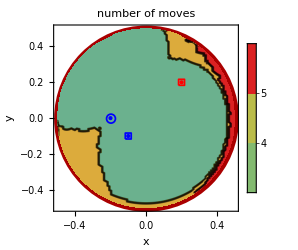

```mathematica
lcp1=ListContourPlot[numMovesCircle,RegionFunction-> Function[{x,y,z}, Norm[{x,y}]< 1/2],InterpolationOrder->1,ImageSize->250,ColorFunctionScaling->False,ColorFunction->ColorData[{"Rainbow",{0,7}}],FrameLabel->{"x","y"},LabelStyle->Directive[Black,Bold,FontSize->12,FontFamily-> "Times"], PlotLabel->"number of moves",PlotLegends->{0,1,2,3,4,5},PlotRange->All];
Vals7a2 = 
Show[lcp1,Prolog->{ Darker[Red], Disk[{0,0},0.52]},Epilog->{(*Darker[Red],Rectangle[-0.025{1,1},{0,1.025}],Rectangle[{-0.025,1-0.0125},{1.025,1.025}],Rectangle[-0.025{1,1},{1.025,0}],Rectangle[{1-0.0125,-0.025},{1.025,1.025}],*) Red,Point[{s1}],EdgeForm[Directive[Red,Thickness[0.005]]],FaceForm[None],Rectangle[s1-2/3r {1,1},s1+2/3r{1,1}], Blue,Point[{s2}],EdgeForm[Directive[Blue,Thickness[0.005]]],FaceForm[None],Rectangle[s2-2/3r {1,1},s2+2/3r{1,1}], Blue,Thickness[0.005],Point[{g2}], Blue,Thickness[0.005], Circle[g2,r]} ]
```

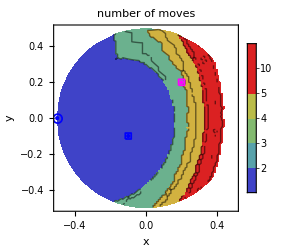
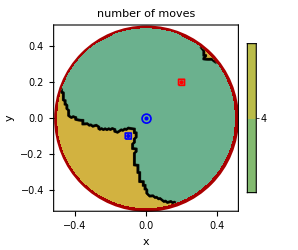

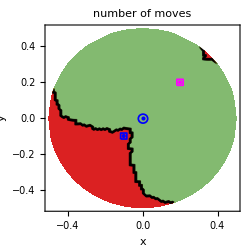

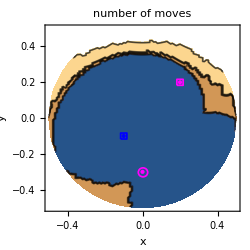

```mathematica
distMovesCircle=Flatten[Table[{x,y,distanceMoved[First@pathToGoal[s1,s2, {x,y},g2,defaultdelta]]},{x,-1/2,1/2,step},{y,-Sqrt[1/4-x^2],Sqrt[1/4-x^2],step}],1];
```

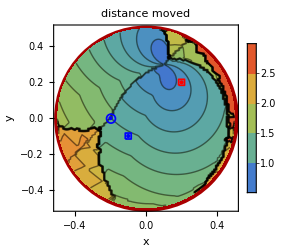

```mathematica
lcp2=ListContourPlot[distMovesCircle,RegionFunction-> Function[{x,y,z}, Norm[{x,y}]< 1/2],InterpolationOrder->1,ImageSize->250,ColorFunctionScaling->False,ColorFunction->ColorData[{"Rainbow",{0,3}}],FrameLabel->{"x","y"},LabelStyle->Directive[Black,Bold,FontSize->12,FontFamily-> "Times"], PlotLabel->"distance moved",PlotLegends->{0,0.5,1,1.5,2,2.5,3},(*PlotRange->All,*)PerformanceGoal->"Quality",Contours->15];
Vals = 
Show[lcp2,Prolog->{ Darker[Red], Disk[{0,0},0.52]},Epilog->{(*Darker[Red],Rectangle[-0.025{1,1},{0,1.025}],Rectangle[{-0.025,1-0.0125},{1.025,1.025}],Rectangle[-0.025{1,1},{1.025,0}],Rectangle[{1-0.0125,-0.025},{1.025,1.025}],*) Red,Point[{s1}],EdgeForm[Directive[Red,Thickness[0.005]]],FaceForm[None],Rectangle[s1-2/3r {1,1},s1+2/3r{1,1}], Blue,Point[{s2}],EdgeForm[Directive[Blue,Thickness[0.005]]],FaceForm[None],Rectangle[s2-2/3r {1,1},s2+2/3r{1,1}], Blue,Thickness[0.005],Point[{g2}], Blue,Thickness[0.005], Circle[g2,r]} ]
```

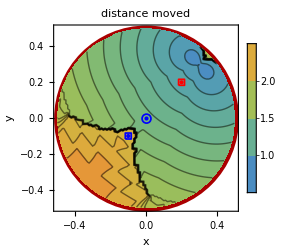

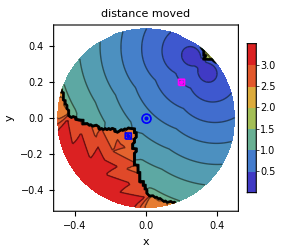
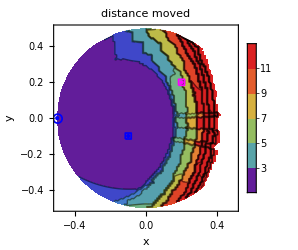

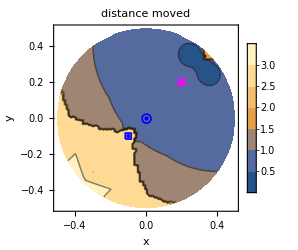
```mathematica
lcp2=ListContourPlot[distMovesCircle,InterpolationOrder->3,ImageSize->250,(*ColorFunctionScaling->False,ColorFunction->ColorData[{"Rainbow",{0,200}}],*)FrameLabel->{"x","y"},LabelStyle->Directive[Black,Bold,FontSize->12,FontFamily-> "Times"], PlotLabel->"distance moved",PlotLegends->Automatic,PlotRange->All,PerformanceGoal->"Quality"];
Vals = 
Show[lcp2,Epilog->{(*Darker[Red],Rectangle[-0.025{1,1},{0,1.025}],Rectangle[{-0.025,1-0.0125},{1.025,1.025}],Rectangle[-0.025{1,1},{1.025,0}],Rectangle[{1-0.0125,-0.025},{1.025,1.025}],*) Magenta,Point[{s1}],EdgeForm[Directive[Magenta,Thickness[0.005]]],FaceForm[None],Rectangle[s1-2/3r {1,1},s1+2/3r{1,1}], Blue,Point[{s2}],EdgeForm[Directive[Blue,Thickness[0.005]]],FaceForm[None],Rectangle[s2-2/3r {1,1},s2+2/3r{1,1}], Blue,Thickness[0.005],Point[{g2}], Blue,Thickness[0.005], Circle[g2,r]} ]
(*Legended[Row[{Vals7a2},Spacer[7]],bl]*)
-Graphics-
```

```mathematica
lcp2=ListDensityPlot[distMovesCircle,RegionFunction-> Function[{x,y,z}, Norm[{x,y}]< 1/2],InterpolationOrder->0,ImageSize->250,(*ColorFunctionScaling->False,ColorFunction->ColorData[{"Rainbow",{0,200}}],*)FrameLabel->{"x","y"},LabelStyle->Directive[Black,Bold,FontSize->12,FontFamily-> "Times"], PlotLabel->"distance moved",PlotLegends->Automatic,PlotRange->All,PerformanceGoal->"Quality"(*, Contours->21*)];
Vals = 
Show[lcp2,Epilog->{(*Darker[Red],Rectangle[-0.025{1,1},{0,1.025}],Rectangle[{-0.025,1-0.0125},{1.025,1.025}],Rectangle[-0.025{1,1},{1.025,0}],Rectangle[{1-0.0125,-0.025},{1.025,1.025}],*) Magenta,Point[{s1}],EdgeForm[Directive[Magenta,Thickness[0.005]]],FaceForm[None],Rectangle[s1-2/3r {1,1},s1+2/3r{1,1}], Blue,Point[{s2}],EdgeForm[Directive[Blue,Thickness[0.005]]],FaceForm[None],Rectangle[s2-2/3r {1,1},s2+2/3r{1,1}], Blue,Thickness[0.005],Point[{g2}], Blue,Thickness[0.005], Circle[g2,r]} ]
```

-Graphics-

```mathematica
lognumMovesCircle = numMovesCircle;
lognumMovesCircle[[;;,3]] = lognumMovesCircle[[;;,3]]^.5;
```

```mathematica
lcp1=ListContourPlot[numMovesCircle,InterpolationOrder->3,ImageSize->250,(*ColorFunctionScaling->False,ColorFunction->ColorData[{"Rainbow",{0,200}}],*)FrameLabel->{"x","y"},LabelStyle->Directive[Black,Bold,FontSize->12,FontFamily-> "Times"], PlotLabel->"number of moves",PlotLegends->Automatic,PlotRange->All,Contours->{3,5,10,15,20,25,30,35,40}];
Vals7a2 = 
Show[lcp1,Epilog->{(*Darker[Red],Rectangle[-0.025{1,1},{0,1.025}],Rectangle[{-0.025,1-0.0125},{1.025,1.025}],Rectangle[-0.025{1,1},{1.025,0}],Rectangle[{1-0.0125,-0.025},{1.025,1.025}],*) Magenta,Point[{s1}],EdgeForm[Directive[Magenta,Thickness[0.005]]],FaceForm[None],Rectangle[s1-2/3r {1,1},s1+2/3r{1,1}], Blue,Point[{s2}],EdgeForm[Directive[Blue,Thickness[0.005]]],FaceForm[None],Rectangle[s2-2/3r {1,1},s2+2/3r{1,1}], Magenta,Thickness[0.005],Point[{g1}], Magenta,Thickness[0.005], Circle[g1,r]} ]
```

-Graphics-

```mathematica
lcp1=ListContourPlot[numMovesCircle,InterpolationOrder->3,ImageSize->250,(*ColorFunctionScaling->False,ColorFunction->ColorData[{"Rainbow",{0,200}}],*)FrameLabel->{"x","y"},LabelStyle->Directive[Black,Bold,FontSize->12,FontFamily-> "Times"], PlotLabel->"number of moves",PlotLegends->Automatic,PlotRange->All,Contours->{3,5,10,15,20,25,30,35,40}];
Vals7a2 = 
Show[lcp1,Epilog->{(*Darker[Red],Rectangle[-0.025{1,1},{0,1.025}],Rectangle[{-0.025,1-0.0125},{1.025,1.025}],Rectangle[-0.025{1,1},{1.025,0}],Rectangle[{1-0.0125,-0.025},{1.025,1.025}],*) Magenta,Point[{s1}],EdgeForm[Directive[Magenta,Thickness[0.005]]],FaceForm[None],Rectangle[s1-2/3r {1,1},s1+2/3r{1,1}], Blue,Point[{s2}],EdgeForm[Directive[Blue,Thickness[0.005]]],FaceForm[None],Rectangle[s2-2/3r {1,1},s2+2/3r{1,1}], Magenta,Thickness[0.005],Point[{g1}], Magenta,Thickness[0.005], Circle[g1,r]} ]
(*Legended[Row[{Vals7a2},Spacer[7]],bl]*)
```

-Graphics-

```mathematica
lcp1=ListContourPlot[numMovesCircle,InterpolationOrder->3,ImageSize->250,(*ColorFunctionScaling->False,ColorFunction->ColorData[{"Rainbow",{0,200}}],*)FrameLabel->{"x","y"},LabelStyle->Directive[Black,Bold,FontSize->12,FontFamily-> "Times"], PlotLabel->"distance moved"];
Vals7a2 = 
Show[lcp1,Epilog->{(*Darker[Red],Rectangle[-0.025{1,1},{0,1.025}],Rectangle[{-0.025,1-0.0125},{1.025,1.025}],Rectangle[-0.025{1,1},{1.025,0}],Rectangle[{1-0.0125,-0.025},{1.025,1.025}],*) Magenta,Point[{s1}],EdgeForm[Directive[Magenta,Thickness[0.005]]],FaceForm[None],Rectangle[s1-2/3r {1,1},s1+2/3r{1,1}], Blue,Point[{s2}],EdgeForm[Directive[Blue,Thickness[0.005]]],FaceForm[None],Rectangle[s2-2/3r {1,1},s2+2/3r{1,1}], Magenta,Thickness[0.005],Point[{g1}], Magenta,Thickness[0.005], Circle[g1,r]} ]
(*Legended[Row[{Vals7a2},Spacer[7]],bl]*)
```

-Graphics-

```mathematica
numMovesCircle
```

{{-0.5,0.,1},{-0.49,-0.0994987,1},{-0.49,-0.0894987,1},{-0.49,-0.0794987,1},{-0.49,-0.0694987,1},{-0.49,-0.0594987,1},{-0.49,-0.0494987,1},{-0.49,-0.0394987,1},{-0.49,-0.0294987,1},{-0.49,-0.0194987,1},{-0.49,-0.00949874,1},{-0.49,0.000501256,1},7878,{0.49,0.000501256,1},{0.49,0.0105013,1},{0.49,0.0205013,1},{0.49,0.0305013,1},{0.49,0.0405013,1},{0.49,0.0505013,1},{0.49,0.0605013,1},{0.49,0.0705013,1},{0.49,0.0805013,1},{0.49,0.0905013,1},{0.5,0.,1}}
 |  |  |  |

```mathematica
s1 = {0.2,0.2};
s2 = {-0.1,-0.1};
g1 = {-1/2,0};
g2 = {1/2,0};
deltaCalc = Table[{δ,Length[First@pathToGoal[s1,s2, g1,g2,δ]]-1},{δ,0.005,0.1,0.005}];
```

```mathematica
ListPlot[deltaCalc,PlotLabel->{"δ","# of moves"},LabelStyle->Directive[Black,Bold,FontSize->12,FontFamily-> "Times"](*, PlotLabel->"distance moved"*)]
```

-Graphics-

```mathematica
{{0.001,1},{0.002,1},{0.003,1},{0.004,1},{0.005,1},{0.006,1},{0.007,1},{0.008,1},{0.009000000000000001,1},{0.010000000000000002,1}}
```

```mathematica
s1 = {0.2,0.2};
s2 = {-0.1,-0.1};
g1 = {-0.5(*+0.001*),0};
g2 = {0.5(*-0.001*),0};
deltaDistCalc2 = Table[{δ,distanceMoved[First@pathToGoal[s1,s2, g1,g2,δ]]},{δ,0.001,0.1,0.001}];
```

$Aborted

```mathematica
Timing[distanceMoved[First@pathToGoal[s1,s2, g1,g2,0.001]]]
(*For 0.003 and 0 epsilon takes 3.539149 s,  with distance 15.359074090459426 
For 0.002 and 0 epsilon it takes 14.65348 s,  15.375990584640471
For 0.0018 and 0 epsilonit takes {16.497414,15.380856175035351}
For 0.0015 and 0 epsilon it takes {19.900618,15.386116543258202}
For 0.00125 and 0 epsilon it takes {22.524758,15.38965195961841}
For 0.001 and 0.001 epsilon it takes {5.998784,35.200477958563496}
}
*)
```

{4.80046,32.8844}

```mathematica
lpDeltaDist = ListPlot[deltaDistCalc2,FrameLabel->{"δ","# of moves"},LabelStyle->Directive[Black,Bold,FontSize->12,FontFamily-> "Times"](*, PlotLabel->"distance moved"*)]
```

-Graphics-

```mathematica
Fit[deltaDistCalc2,{1,1/x},x]
fitDeltaDist = Plot[%,{x,0.001,0.1},PlotRange->All,PlotStyle->Red(*,AxesOrigin->{0,0}*)];
Show[{fitDeltaDist,lpDeltaDist}]
```

5.50212+0.0316755/x

-Graphics-

```mathematica
pathToGoal[s1,s2, g1,g2,0.001]
```

$Aborted

```mathematica
s1 = {0.2,0.2};
s2 = {-0.1,-0.1};
g1 = {-1/2,0};
g2 = {1/2,0};
δres = pathToGoal[s1,s2, g1,g2,0.001][[4]]
```

{0.575736,0.528547,0.357997,0.254484,0.179585,0.131024,0.1008,0.0798266,0.065691,0.0550087,0.0468222,0.0408482,0.0362854,0.0326534,0.0295703,0.0267765,0.0243127,0.0222593,0.020549,0.0191004,0.0178542,0.0167696,0.015816,0.0149702,0.0142141,0.0135341,0.0129185,0.0123591,0.0118482,0.0113792,0.0109468,0.0105474,0.0101766,0.00983178,0.00951091,0.00921074,0.00892909,0.0086652,0.00841638,0.00818187,0.00796007,0.00775075,0.00755183,0.0073632,0.00718444,0.00701419,0.00685169,0.00669691,0.00654896,0.00640756,0.00627262,0.00614311,0.00601873,0.00589964,0.00578521,0.00567482,0.00556888,0.00546689,0.00536878,0.00527426,0.00518267,0.00509469,0.0050096,0.00492747,0.00484822,0.00477098,0.00469642,0.00462451,0.00455474,0.00448678,0.00442091,0.00435684,0.0042947,0.00423458,0.0041761,0.00411881,0.00406336,0.00400905,0.0039565,0.00390573,0.00385601,0.00380736,0.0037597,0.00371368,0.00366884,0.00362496,0.00358197,0.00354,0.003499,0.00345895,0.00341993,0.00338174,0.00334465,0.00330839,0.00327228,0.00323701,0.00320271,0.00316941,0.00313622,0.00310393,0.00307262,0.00304208,0.0030117,0.00298231,0.00295299,0.0029246,0.00289705,0.00286959,0.00284309,0.00281663,0.00279107,0.00276559,0.00274108,0.00271646,0.00269197,0.0026684,0.00264477,0.00262213,0.00259955,0.0025779,0.00255627,0.00253475,0.00251404,0.00249332,0.00247281,0.00245308,0.00243337,0.00241372,0.00239493,0.00237621,0.00235755,0.00233976,0.00232204,0.00230438,0.00228671,0.00226992,0.00225319,0.00223652,0.00222073,0.00220488,0.00218914,0.00217346,0.00215762,0.00214281,0.00212807,0.00211322,0.00209848,0.00208368,0.00206982,0.00205597,0.00204222,0.00202842,0.00201467,0.00200176,0.00198895,0.00197615,0.00196324,0.00195048,0.00193768,0.00192571,0.0019139,0.00190209,0.00189023,0.00187836,0.0018666,0.00185564,0.00184472,0.00183386,0.00182299,0.00181213,0.00180126,0.00179049,0.00177963,0.00176966,0.00175974,0.00174987,0.00174001,0.00173014,0.00172026,0.00171039,0.00170048,0.0016906,0.00168164,0.00167272,0.00166384,0.00165497,0.0016461,0.00163723,0.0016283,0.00161943,0.00161055,0.00160259,0.00159458,0.00158665,0.00157878,0.0015709,0.00156298,0.00155502,0.00154709,0.00153921,0.00153133,0.00152345,0.00151552,0.00150848,0.00150063,0.00149367,0.00148674,0.00147979,0.00147285,0.00146597,0.00145897,0.00145208,0.00144515,0.00143827,0.00143131,0.00142438,0.00141744,0.00141048,0.00140355,0.00139759,0.00139158,0.00138565,0.00137976,0.0013738,0.00136787,0.00136186,0.00135593,0.00135004,0.00134408,0.00133815,0.00133218,0.00132625,0.00132031,0.00131435,0.00130842,0.00130246,0.00129652,0.00129156,0.00128655,0.00128161,0.00127661,0.00127167,0.00126671,0.00126177,0.00125681,0.00125188,0.00124687,0.00124198,0.00123697,0.00123203,0.00122707,0.00122213,0.00121717,0.00121223,0.00120723,0.00120229,0.00119732,0.00119238,0.00118742,0.00118248,0.00117748,0.00117257,0.00116851,0.0011645,0.00116056,0.00115656,0.00115262,0.00114866,0.00114465,0.00114071,0.00113675,0.0011328,0.0011288,0.0011248,0.00112089,0.00111689,0.00111295,0.00110899,0.00110498,0.00110104,0.00109703,0.00109309,0.00108913,0.00108512,0.00108118,0.00107722,0.00107327,0.00106927,0.00106526,0.00106136,0.00105735,0.00105341,0.00104944,0.00104544,0.00104149,0.00103749,0.00103354,0.00103052,0.00102752,0.00102457,0.00102157,0.00101857,0.00101556,0.00101262,0.00100965,0.00100665,0.0010037,0.0010007,0.000997736}

```mathematica
deltanum = ListPlot[δres, LabelStyle->Directive[Black,Bold,FontSize->12,FontFamily-> "Times"],Frame -> True, FrameLabel->{ "# of moves", δ}]
```

-Graphics-

{0,1.21977,1.77293,2.59006,3.29197,3.88288,4.3861,4.82769,5.2215,5.58002,5.90601,6.20525,6.48468,6.74963,7.00294,7.24495,7.47509,7.69334,7.90051,8.09808,8.28741,8.46952,8.64521,8.81519,8.98002,9.14016,9.29601,9.44792,9.59612,9.7409,9.88258,10.0213,10.1574,10.2908,10.4218,10.5502,10.6766,10.8009,10.9232,11.0436,11.1624,11.2794,11.3947,11.5085,11.6207,11.7314,11.8408,11.949,12.0558,12.1614,12.2657,12.3688,12.4709,12.5719,12.6717,12.7707,12.8688,12.9658,13.0618,13.1569,13.2512,13.3447,13.4371,13.5286,13.6192,13.7093,13.7989,13.8875,13.975,14.0621,14.1486,14.2345,14.3199,14.4044,14.4881,14.5716,14.6546,14.7371,14.8191,14.9,14.9802,15.0602,15.1401,15.2193,15.2975,15.3753,15.4529,15.5301,15.6068,15.6831,15.7589,15.8342,15.9089,15.9828,16.057,16.1314,16.2051,16.2778,16.3505,16.4233,16.4951,16.5661,16.6369,16.7073,16.7777,16.8479,16.917,16.9859,17.0544,17.1226,17.1905,17.2581,17.3253,17.3921,17.4599,17.5271,17.594,17.6605,17.7262,17.7913,17.8558,17.921,17.9857,18.0499,18.1145,18.1785,18.242,18.3061,18.3694,18.4318,18.4948,18.5569,18.6181,18.6798,18.7422,18.8038,18.8644,18.9254,18.9855,19.0446,19.1042,19.1642,19.2251,19.2849,19.3431,19.4021,19.4617,19.5218,19.5808,19.6383,19.6961,19.7545,19.8135,19.8712,19.9274,19.9839,20.0411,20.0989,20.157,20.2139,20.2689,20.3241,20.3799,20.4364,20.4932,20.5484,20.6019,20.6556,20.7097,20.7642,20.8192,20.8745,20.9305,20.9849,21.0372,21.0895,21.1422,21.1954,21.2491,21.3032,21.358,21.4133,21.4663,21.517,21.5678,21.6189,21.6704,21.7225,21.7751,21.8283,21.8818,21.933,21.9818,22.0306,22.0794,22.1285,22.1781,22.2285,22.2791,22.3299,22.3811,22.4327,22.4849,22.5347,22.5845,22.6343,22.6815,22.7289,22.7766,22.8244,22.8728,22.9216,22.9704,23.0198,23.0696,23.1199,23.1705,23.2217,23.2732,23.3212,23.3661,23.411,23.4557,23.501,23.5467,23.5928,23.6393,23.6856,23.7325,23.7798,23.8274,23.8753,23.9235,23.9722,24.0212,24.0706,24.1202,24.166,24.208,24.2501,24.2925,24.3351,24.3778,24.4208,24.464,24.5075,24.5515,24.5956,24.6399,24.6847,24.7296,24.7748,24.8203,24.8661,24.9123,24.9589,25.0056,25.0526,25.0999,25.1006,25.1008,25.1009,25.101,25.1012,25.1014,25.1015,25.1017,25.1018,25.102,25.1021,25.1023,25.1024,25.1025,25.1027,25.1028,25.103,25.1031,25.1033,25.1034,25.1036,25.1037,25.1039,25.104,25.1041,25.1042,25.1044,25.1045,25.1047,25.1048,25.105,25.105,25.1052,25.1053,25.1055,25.1056,25.1057,25.1058,25.106,25.1061,25.1062,25.1063,25.1065,25.1066,25.1068,25.1068,25.107,25.1071,25.1072,25.1073}

```mathematica
model=a/(x^b);
fit= FindFit[δres[[3;;-1]], model, {a,b},x]
modelf=Function[{t},Evaluate[model/.fit]];
fittedNum = Plot[modelf[x],{x,10,50},PlotRange->{{0,50},{0,0.6}},PlotStyle->Red(*,AxesOrigin->{0,0}*)];
deltanum = ListPlot[δres, LabelStyle->Directive[Black,Bold,FontSize->12,FontFamily-> "Times"],PlotRange->{{0,50},{0,0.6}},Frame-> True,FrameLabel->{ "number of moves", δ}];
Show[{deltanum,fittedNum }]
```

{a→0.394977,b→0.947229}

-Graphics-

```mathematica
fittedNum
```

-Graphics-

```mathematica
Fit[δres,{1,1/x},x]
fitDeltaNum = Plot[%,{x,5,50},PlotRange->{{0,300},{0,0.6}},Frame -> True, LabelStyle->Directive[Black,Bold,FontSize->12,FontFamily-> "Times"],FrameLabel->{ "number of moves", δ},PlotStyle->Red(*,AxesOrigin->{0,0}*)];
Show[{fitDeltaNum,deltanum}]
```

-0.00329914+0.715736/x

-Graphics-

```mathematica
-0.0032991386642104233+0.7157362070480862/x
```

-0.00329914+0.715736/x

```mathematica
s1 = {0.2,0.2};
s2 = {-0.1,-0.1};
g1 = {-1/2,0};
g2 = {1/2,0};
dist = Last@pathToGoal[s1,s2, g1,g2,0.001]
```

```mathematica
δres={0,1.2197700166988688,1.7729325600729582,2.590056065255893,3.291973348640438,3.8828825319429336,4.386097974106599,4.827687687288541,5.22149556652927,5.580015464527042,5.9060071201134825,6.205253069318239,6.484679307488037,6.749629850130473,7.002938758342786,7.244945335957466,7.475091811396814,7.693337718769662,7.9005055108987445,8.098075696947866,8.287406056495332,8.469516910395683,8.645211573997862,8.815186596458153,8.980017228201984,9.140158944101636,9.296013596988542,9.44792038666863,9.59612196087259,9.74089585233111,9.882582781851138,10.021349415422899,10.157362582440786,10.290846845390334,10.421759574982815,10.550234956422294,10.676629067283875,10.800923703639967,10.923197633287105,11.043643538697376,11.162384214297123,11.279352182222642,11.394661011638895,11.508538342385554,11.620745630792573,11.731388402355009,11.84082534244573,11.948990751042691,12.05581076360337,12.161432000006712,12.265728170466982,12.36878743366438,12.470886158396503,12.571894997000513,12.671743170985144,12.77074662915394,12.86882676103432,12.965821493491472,13.06183396835267,13.156880818932319,13.2512344796523,13.344688665298557,13.437090532715716,13.528632354355933,13.619223307688527,13.709329341207342,13.798937617909605,13.887454450025178,13.975020078360593,14.062070309406158,14.148581199937121,14.234516964844374,14.319877478662747,14.404384996846971,14.488121180994174,14.571581934071075,14.654561909725315,14.737061219291935,14.819095366055265,14.900005989118014,14.980178097061073,15.060184616398129,15.140115368197279,15.219347343013894,15.297549339924714,15.375315521788028,15.452865919897429,15.53006261318814,15.606805971903873,15.683133190161026,15.758938226643746,15.83423992606691,15.908892215518739,15.982848356320591,16.05703029465849,16.131433004395085,16.20512840181494,16.277822566882918,16.35048556123579,16.423278997853387,16.495143979837625,16.566050700048983,16.63685902428979,16.707347686027113,16.777679829425807,16.847893201925583,16.916976157512273,16.985867292431635,17.05437427432747,17.12256925038718,17.19050622469295,17.258110404216836,17.325257357161462,17.39213496436395,17.45986191081429,17.52710076483867,17.594040299423625,17.660471323502755,17.726221878599013,17.791321004435858,17.855833589491105,17.921019547186724,17.985681767360408,18.049859655406742,18.114537291392594,18.178535197273135,18.241993185507518,18.306076615358933,18.369399447069306,18.431844623438927,18.494802695384827,18.55693285275141,18.618119010783275,18.679803344100712,18.742204497699916,18.803789037715873,18.864351847258604,18.925420737049095,18.985479090716392,19.04459517440634,19.104174857472803,19.1641571678968,19.225082786256795,19.28488824730648,19.34311805561845,19.402072416125794,19.461673293960978,19.5218434139624,19.580800886181848,19.638314507832423,19.696149508549663,19.754514210309882,19.813541897610875,19.87123732153225,19.927385510695313,19.98385937912039,20.041130118707677,20.098861266528704,20.157022856189172,20.213880868257213,20.268875304862494,20.32405565270286,20.379899517725086,20.436362613668184,20.493166583089724,20.548364548145987,20.601913753210123,20.655615630888953,20.709666254343844,20.764189442867835,20.819183933607786,20.874523504977226,20.930518549020345,20.984913404825413,21.03716799257236,21.0895441926784,21.142247670965098,21.195426438641416,21.249096932260105,21.30324923584575,21.35801963011609,21.413306444852978,21.46634498694241,21.517019189882525,21.56779873993185,21.618889907135994,21.670448106591536,21.72248096221536,21.775139796911812,21.82829838479052,21.881821488095092,21.932996170291467,21.981753016042465,22.0305785505874,22.079360484958837,22.128451345467607,22.17814702631813,22.22847998438769,22.279136714214093,22.32993738784168,22.38106742096974,22.43266862924961,22.484921968644926,22.53471900869635,22.584474358615424,22.634327573876142,22.6814798820916,22.72889434837648,22.776591825483234,22.824402599763026,22.872833565251362,22.92157470837721,22.970443357273723,23.01977692636825,23.069607836266677,23.11992256313367,23.17054952286259,23.22169000818559,23.27315479934161,23.32122561765537,23.366056798486497,23.410950434443947,23.45574031371408,23.500982518655427,23.54666817047756,23.59281986824471,23.639258422245067,23.68561674930922,23.732475539539504,23.779790596370297,23.827398130902917,23.875302160767703,23.923499826759446,23.972212542710643,24.021234141989545,24.07056741221859,24.120216740170612,24.165991077203806,24.208041042705762,24.250148164550893,24.292504893853035,24.335129147264414,24.377847737054104,24.42082365296962,24.46404987227394,24.507547588460994,24.55150969477676,24.59556674828886,24.639914137406333,24.68472757708247,24.72962712966197,24.774817136073437,24.820308591625725,24.86608813761959,24.91234716485446,24.958918829528294,25.005618350231895,25.052619762351053,25.099925541124744,25.10063420094785,25.10083451966628,25.10094178084295,25.10104473157537,25.101240512767824,25.101352315035285,25.10154551252872,25.10165525450466,25.101846641749937,25.10195523298145,25.102146229593448,25.102253186140743,25.1024419382356,25.102546812627757,25.102734671120697,25.102837559920523,25.103022901625046,25.103123791789592,25.103307831928817,25.103407582924454,25.103591221332074,25.103689338550787,25.10387119719175,25.10396726546627,25.104147450085136,25.10424155549412,25.104420056060967,25.104512579003625,25.104689386174194,25.10477990885152,25.104956352745567,25.10504616852442,25.105220911222627,25.105308280538303,25.10548137655829,25.10556776433841,25.105739275159262,25.10582520886954,25.10599546217687,25.106089386139985,25.106249285168246,25.106342673736933,25.106501363470635,25.106593441427663,25.106751446315826,25.10684257501628,25.106998997884716,25.10708840312697,25.10724327021592,25.107331332945623};
```

```mathematica
data
```

```mathematica
data={{1.2197700166988688,0.5285465499182342},{1.7729325600729582,0.3579966918869427},{2.590056065255893,0.25448399369228836},{3.291973348640438,0.17958491726041137},{3.8828825319429336,0.13102434539861363},{4.386097974106599,0.10079967732313733},{4.827687687288541,0.07982663910395671},{5.22149556652927,0.06569101111195563},{5.580015464527042,0.05500873843178966},{5.9060071201134825,0.046822220578658036},{6.205253069318239,0.040848240965759564},{6.484679307488037,0.03628538777657109},{6.749629850130473,0.03265340453804122},{7.002938758342786,0.02957034717811724},{7.244945335957466,0.02677654771681548},{7.475091811396814,0.024312690942746462},{7.693337718769662,0.022259322474211807},{7.9005055108987445,0.020549020165649967},{8.098075696947866,0.019100362461917597},{8.287406056495332,0.017854224053324597},{8.469516910395683,0.01676962365613688},{8.645211573997862,0.01581603715682567},{8.815186596458153,0.014970229240166333},{8.980017228201984,0.014214113743909573},{9.140158944101636,0.01353405929982976},{9.296013596988542,0.012918506670962282},{9.44792038666863,0.012359134850857822},{9.59612196087259,0.01184821952214632},{9.74089585233111,0.011379181387174642},{9.882582781851138,0.010946771464897864},{10.021349415422899,0.010547354751279991},{10.157362582440786,0.010176573856678806},{10.290846845390334,0.009831781609883294},{10.421759574982815,0.009510905973286299},{10.550234956422294,0.009210738229271653},{10.676629067283875,0.008929094027513407},{10.800923703639967,0.008665199781541122},{10.923197633287105,0.00841638276480472},{11.043643538697376,0.008181873626460279},{11.162384214297123,0.007960069790954316},{11.279352182222642,0.007750746152971555},{11.394661011638895,0.007551825085111208},{11.508538342385554,0.007363199542174792},{11.620745630792573,0.007184442743802921},{11.731388402355009,0.007014194645380889},{11.84082534244573,0.006851686937724644},{11.948990751042691,0.006696906668642977},{12.05581076360337,0.00654896083737766},{12.161432000006712,0.006407559992744005},{12.265728170466982,0.0062726210007805205},{12.36878743366438,0.006143107968352157},{12.470886158396503,0.006018729895583053},{12.571894997000513,0.00589964163944634},{12.671743170985144,0.005785213413631474},{12.77074662915394,0.0056748170975861045},{12.86882676103432,0.005568882278012777},{12.965821493491472,0.0054668915569906495},{13.06183396835267,0.005368776677420528},{13.156880818932319,0.0052742553149800475},{13.2512344796523,0.0051826683120980155},{13.344688665298557,0.005094694594071858},{13.437090532715716,0.005009598858704445},{13.528632354355933,0.004927472265770061},{13.619223307688527,0.004848224281397084},{13.709329341207342,0.004770975356162777},{13.798937617909605,0.0046964201800956396},{13.887454450025178,0.004624505931149936},{13.975020078360593,0.004554738109305845},{14.062070309406158,0.004486779140963182},{14.148581199937121,0.004420914495856354},{14.234516964844374,0.004356843979402503},{14.319877478662747,0.004294696636364392},{14.404384996846971,0.0042345820607284645},{14.488121180994174,0.004176103414688659},{14.571581934071075,0.004118807708128114},{14.654561909725315,0.004063364797879387},{14.737061219291935,0.004009052273978964},{14.819095366055265,0.003956498286021293},{14.900005989118014,0.0039057284749055565},{14.980178097061073,0.0038560074114433185},{15.060184616398129,0.003807364153222692},{15.140115368197279,0.0037597018958627215},{15.219347343013894,0.003713682760165482},{15.297549339924714,0.0036688421784746295},{15.375315521788028,0.0036249612195142777},{15.452865919897429,0.0035819744796876662},{15.53006261318814,0.0035400036690100833},{15.606805971903873,0.003499004829734864},{15.683133190161026,0.0034589453081809163},{15.758938226643746,0.0034199337156129994},{15.83423992606691,0.003381742531124554},{15.908892215518739,0.0033446451766363516},{15.982848356320591,0.003308385348355092},{16.05703029465849,0.003272282233275914},{16.131433004395085,0.003237006769715056},{16.20512840181494,0.0032027092952077174},{16.277822566882918,0.003169414868645637},{16.35048556123579,0.003136223059108989},{16.423278997853387,0.0031039251335605034},{16.495143979837625,0.003072617509853548},{16.566050700048983,0.003042079856055091},{16.63685902428979,0.0030117010661599997},{16.707347686027113,0.002982313166012718},{16.777679829425807,0.002952990621510998},{16.847893201925583,0.002924599967349173},{16.916976157512273,0.0028970465730853157},{16.985867292431635,0.002869585933306662},{17.05437427432747,0.002843091826746802},{17.12256925038718,0.0028166296502022403},{17.19050622469295,0.002791068171187794},{17.258110404216836,0.0027655942783663123},{17.325257357161462,0.002741080703006049},{17.39213496436395,0.0027164606915035527},{17.45986191081429,0.0026919721347454795},{17.52710076483867,0.0026683997277987537},{17.594040299423625,0.002644768812317677},{17.660471323502755,0.00262213179556825},{17.726221878599013,0.002599549252846778},{17.791321004435858,0.0025779043486053865},{17.855833589491105,0.0025562665565792564},{17.921019547186724,0.00253475246494117},{17.985681767360408,0.002514036578226908},{18.049859655406742,0.0024933247592807684},{18.114537291392594,0.002472806207707179},{18.178535197273135,0.002453083003805423},{18.241993185507518,0.002433370405440116},{18.306076615358933,0.0024137190155257837},{18.369399447069306,0.002394926731956626},{18.431844623438927,0.002376213943944716},{18.494802695384827,0.002357553749726904},{18.55693285275141,0.0023397635209566614},{18.618119010783275,0.002322042366230903},{18.679803344100712,0.0023043809448988206},{18.742204497699916,0.0022867097965508787},{18.803789037715873,0.0022699200568148115},{18.864351847258604,0.0022531886654837407},{18.925420737049095,0.002236515965317043},{18.985479090716392,0.002220727183818161},{19.04459517440634,0.0022048778529062396},{19.104174857472803,0.002189144369008411},{19.1641571678968,0.0021734616811318608},{19.225082786256795,0.0021576171769923658},{19.28488824730648,0.0021428144909489966},{19.34311805561845,0.0021280717272516014},{19.402072416125794,0.0021132220582349426},{19.461673293960978,0.00209848319128747},{19.5218434139624,0.0020836839974394117},{19.580800886181848,0.0020698227734813335},{19.638314507832423,0.0020559676371950664},{19.696149508549663,0.0020422204849842585},{19.754514210309882,0.0020284216021763113},{19.813541897610875,0.0020146712399584654},{19.87123732153225,0.0020017614545204676},{19.927385510695313,0.001988954688968758},{19.98385937912039,0.001976149603716837},{20.041130118707677,0.001963236550206804},{20.098861266528704,0.0019504830954729657},{20.157022856189172,0.0019376756030146103},{20.213880868257213,0.0019257122610094601},{20.268875304862494,0.0019138963869950176},{20.32405565270286,0.0019020898246779883},{20.379899517725086,0.001890227022179114},{20.436362613668184,0.0018783637756600857},{20.493166583089724,0.0018665986544418312},{20.548364548145987,0.0018556383106062002},{20.601913753210123,0.0018447210964639416},{20.655615630888953,0.0018338584477254338},{20.709666254343844,0.0018229899803414717},{20.764189442867835,0.0018121263299616386},{20.819183933607786,0.001801262148493743},{20.874523504977226,0.0017904869839006077},{20.930518549020345,0.0017796262067288904},{20.984913404825413,0.0017696584177934183},{21.03716799257236,0.0017597406234545199},{21.0895441926784,0.0017498710622941838},{21.142247670965098,0.0017400059085497244},{21.195426438641416,0.0017301352626498678},{21.249096932260105,0.001720264092462842},{21.30324923584575,0.0017103923941066412},{21.35801963011609,0.0017004770615741682},{21.413306444852978,0.0016906043739985943},{21.46634498694241,0.0016816394667377166},{21.517019189882525,0.0016727158763838457},{21.56779873993185,0.0016638442220683336},{21.618889907135994,0.0016549719613903058},{21.670448106591536,0.001646099090405695},{21.72248096221536,0.0016372256051383483},{21.775139796911812,0.0016283045649841954},{21.82829838479052,0.0016194299885551322},{21.881821488095092,0.0016105547868728864},{21.932996170291467,0.0016025877811983724},{21.981753016042465,0.0015945784606593572},{22.0305785505874,0.0015866535687769634},{22.079360484958837,0.0015787792092080144},{22.128451345467607,0.0015708999467429763},{22.17814702631813,0.0015629780511865476},{22.22847998438769,0.0015550196986499065},{22.279136714214093,0.001547093177584724},{22.32993738784168,0.0015392123322146567},{22.38106742096974,0.0015313308738026388},{22.43266862924961,0.0015234527801781805},{22.484921968644926,0.0015155245984257437},{22.53471900869635,0.001508483939611227},{22.584474358615424,0.0015006349915480666},{22.634327573876142,0.0014936740647657487},{22.6814798820916,0.001486742624995263},{22.72889434837648,0.0014797856349078042},{22.776591825483234,0.001472853773604177},{22.824402599763026,0.001465970472271927},{22.872833565251362,0.0014589683112326002},{22.92157470837721,0.0014520806635697214},{22.970443357273723,0.0014451513873336985},{23.01977692636825,0.001438266305760827},{23.069607836266677,0.001431308961455935},{23.11992256313367,0.0014243750396654153},{23.17054952286259,0.0014174444610092207},{23.22169000818559,0.001410483349393865},{23.27315479934161,0.001403552284755083},{23.32122561765537,0.0013975889406907527},{23.366056798486497,0.0013915814802365478},{23.410950434443947,0.0013856477421368973},{23.45574031371408,0.0013797610813287564},{23.500982518655427,0.0013738012749492379},{23.54666817047756,0.0013678699593761001},{23.59281986824471,0.0013618628799104693},{23.639258422245067,0.001355931294853674},{23.68561674930922,0.001350042740458468},{23.732475539539504,0.0013440793738228596},{23.779790596370297,0.0013381466857662616},{23.827398130902917,0.001332183353886962},{23.875302160767703,0.0013262501400644888},{23.923499826759446,0.001320313372036086},{23.972212542710643,0.0013143530976109652},{24.021234141989545,0.0013084158390699319},{24.07056741221859,0.0013024555525762427},{24.120216740170612,0.001296517799127761},{24.165991077203806,0.0012915553868868557},{24.208041042705762,0.0012865503173359327},{24.250148164550893,0.0012816131371400363},{24.292504893853035,0.0012766112150399689},{24.335129147264414,0.0012716737484032015},{24.377847737054104,0.0012667112472507513},{24.42082365296962,0.0012617732667182802},{24.46404987227394,0.0012568137549757719},{24.507547588460994,0.0012518752211553297},{24.55150969477676,0.0012468734825324956},{24.59556674828886,0.001241976536128675},{24.639914137406333,0.0012369719394821344},{24.68472757708247,0.0012320325888819372},{24.72962712966197,0.0012270727373936419},{24.774817136073437,0.0012221328227809414},{24.820308591625725,0.0012171700283983844},{24.86608813761959,0.001212229580305424},{24.91234716485446,0.0012072281009022356},{24.958918829528294,0.0012022873526893463},{25.005618350231895,0.001197324361000618},{25.052619762351053,0.0011923830723115092},{25.099925541124744,0.0011874200385956213},{25.10063420094785,0.0011824782048904803},{25.10083451966628,0.0011774768980883366},{25.10094178084295,0.0011725727438285372},{25.10104473157537,0.0011685080487697785},{25.101240512767824,0.0011645021895285712},{25.101352315035285,0.0011605607107142424},{25.10154551252872,0.0011565575943232043},{25.10165525450466,0.0011526158189710811},{25.101846641749937,0.0011486561110245486},{25.10195523298145,0.0011446504500550736},{25.102146229593448,0.0011407081051156842},{25.102253186140743,0.001136748318109837},{25.1024419382356,0.0011328027700155952},{25.102546812627757,0.001128802447478372},{25.102734671120697,0.0011247969837653304},{25.102837559920523,0.0011208939193398937},{25.103022901625046,0.001116893654221851},{25.103123791789592,0.0011129472922477568},{25.103307831928817,0.0011089870254790135},{25.103407582924454,0.0011049818378545684},{25.103591221332074,0.001101037420517259},{25.103689338550787,0.0010970347482287535},{25.10387119719175,0.0010930900233176999},{25.10396726546627,0.0010891270051368585},{25.104147450085136,0.0010851244297526152},{25.10424155549412,0.0010811791088291},{25.104420056060967,0.0010772160384729945},{25.104512579003625,0.0010732700937485795},{25.104689386174194,0.001069267637308191},{25.10477990885152,0.001065262830965974},{25.104956352745567,0.0010613556562241167},{25.10504616852442,0.0010573532912503403},{25.105220911222627,0.0010534064584883929},{25.105308280538303,0.0010494429910837821},{25.10548137655829,0.0010454407221848205},{25.10556776433841,0.0010414910363476526},{25.105739275159262,0.0010374887884134765},{25.10582520886954,0.0010335410553391489},{25.10599546217687,0.0010305214736993085},{25.106089386139985,0.0010275176007660258},{25.106249285168246,0.0010245702021570713},{25.106342673736933,0.0010215685858963042},{25.106501363470635,0.0010185669727323932},{25.106593441427663,0.0010155631423917066},{25.106751446315826,0.0010126154681078248},{25.10684257501628,0.0010096523584328665},{25.106998997884716,0.0010066508141912678},{25.10708840312697,0.0010037024703549724},{25.10724327021592,0.0010007009420427426},{25.107331332945623,0.0009977356058367137}};
```

```mathematica
(*data=Transpose@{dist,δres}*)
model=a/(x^b);
fit= FindFit[data[[5;;-1]], model, {a,b},x]
modelf=Function[{t},Evaluate[model/.fit]];
fittedNum = Plot[modelf[x],{x,0.01,25},PlotRange->{{0,25},{0,0.6}},PlotStyle->Red(*,AxesOrigin->{0,0}*)];
datadist = ListPlot[data, LabelStyle->Directive[Black,Bold,FontSize->12,FontFamily-> "Times"],Frame-> True,FrameLabel->{ distance moved, δ},PlotRange->All];
Show[{datadist,fittedNum }]
```

{a→4.71634,b→2.61551}

-Graphics-

```mathematica
(*data=Transpose@{dist,δres}*)
model=a/(x^3);
fit= FindFit[data[[5;;-1]], model, {a},x]
modelf=Function[{t},Evaluate[model/.fit]];
fittedNum = Plot[modelf[x],{x,5,25},PlotRange->{{0,25},{0,0.6}},PlotStyle->Red(*,AxesOrigin->{0,0}*)];
datadist = ListPlot[data, LabelStyle->Directive[Black,Bold,FontSize->12,FontFamily-> "Times"],Frame-> True,FrameLabel->{ distance moved, δ},PlotRange->All];
Show[{datadist,fittedNum }]
```

{a→8.66382}

-Graphics-

```mathematica
model=a/(x^3);
fit= FindFit[δres[[5;;-1]], model, {a},x]
modelf=Function[{t},Evaluate[model/.fit]];
(*fittedNum = Plot[modelf[x],{x,5,25},PlotRange->{{0,25},{0,0.6}},PlotStyle->Red(*,AxesOrigin->{0,0}*)];
datadist = ListPlot[data, LabelStyle->Directive[Black,Bold,FontSize->12,FontFamily-> "Times"],Frame-> True,FrameLabel->{ distance moved, δ},PlotRange->All];
Show[{datadist,fittedNum }]*)

fitDeltaNum = Plot[modelf[x],{x,5,25},PlotRange->{{0,50},{0,0.6}},Frame -> True, LabelStyle->Directive[Black,Bold,FontSize->12,FontFamily-> "Times"],FrameLabel->{ "number of moves", δ},PlotStyle->Red(*,AxesOrigin->{0,0}*)];
deltanum = ListPlot[δres, LabelStyle->Directive[Black,Bold,FontSize->12,FontFamily-> "Times"],Frame -> True, FrameLabel->{ "number of moves", δ}];
Show[{fitDeltaNum,deltanum}]
```

{a→4.09524}

-Graphics-

```mathematica
datadist
```

-Graphics-

```mathematica
data={{1.2197700166988688,0.5285465499182342},{1.7729325600729582,0.3579966918869427},{2.590056065255893,0.25448399369228836},{3.291973348640438,0.17958491726041137},{3.8828825319429336,0.13102434539861363},{4.386097974106599,0.10079967732313733},{4.827687687288541,0.07982663910395671},{5.22149556652927,0.06569101111195563},{5.580015464527042,0.05500873843178966},{5.9060071201134825,0.046822220578658036},{6.205253069318239,0.040848240965759564},{6.484679307488037,0.03628538777657109},{6.749629850130473,0.03265340453804122},{7.002938758342786,0.02957034717811724},{7.244945335957466,0.02677654771681548},{7.475091811396814,0.024312690942746462},{7.693337718769662,0.022259322474211807},{7.9005055108987445,0.020549020165649967},{8.098075696947866,0.019100362461917597},{8.287406056495332,0.017854224053324597},{8.469516910395683,0.01676962365613688},{8.645211573997862,0.01581603715682567},{8.815186596458153,0.014970229240166333},{8.980017228201984,0.014214113743909573},{9.140158944101636,0.01353405929982976},{9.296013596988542,0.012918506670962282},{9.44792038666863,0.012359134850857822},{9.59612196087259,0.01184821952214632},{9.74089585233111,0.011379181387174642},{9.882582781851138,0.010946771464897864},{10.021349415422899,0.010547354751279991},{10.157362582440786,0.010176573856678806},{10.290846845390334,0.009831781609883294},{10.421759574982815,0.009510905973286299},{10.550234956422294,0.009210738229271653},{10.676629067283875,0.008929094027513407},{10.800923703639967,0.008665199781541122},{10.923197633287105,0.00841638276480472},{11.043643538697376,0.008181873626460279},{11.162384214297123,0.007960069790954316},{11.279352182222642,0.007750746152971555},{11.394661011638895,0.007551825085111208},{11.508538342385554,0.007363199542174792},{11.620745630792573,0.007184442743802921},{11.731388402355009,0.007014194645380889},{11.84082534244573,0.006851686937724644},{11.948990751042691,0.006696906668642977},{12.05581076360337,0.00654896083737766},{12.161432000006712,0.006407559992744005},{12.265728170466982,0.0062726210007805205},{12.36878743366438,0.006143107968352157},{12.470886158396503,0.006018729895583053},{12.571894997000513,0.00589964163944634},{12.671743170985144,0.005785213413631474},{12.77074662915394,0.0056748170975861045},{12.86882676103432,0.005568882278012777},{12.965821493491472,0.0054668915569906495},{13.06183396835267,0.005368776677420528},{13.156880818932319,0.0052742553149800475},{13.2512344796523,0.0051826683120980155},{13.344688665298557,0.005094694594071858},{13.437090532715716,0.005009598858704445},{13.528632354355933,0.004927472265770061},{13.619223307688527,0.004848224281397084},{13.709329341207342,0.004770975356162777},{13.798937617909605,0.0046964201800956396},{13.887454450025178,0.004624505931149936},{13.975020078360593,0.004554738109305845},{14.062070309406158,0.004486779140963182},{14.148581199937121,0.004420914495856354},{14.234516964844374,0.004356843979402503},{14.319877478662747,0.004294696636364392},{14.404384996846971,0.0042345820607284645},{14.488121180994174,0.004176103414688659},{14.571581934071075,0.004118807708128114},{14.654561909725315,0.004063364797879387},{14.737061219291935,0.004009052273978964},{14.819095366055265,0.003956498286021293},{14.900005989118014,0.0039057284749055565},{14.980178097061073,0.0038560074114433185},{15.060184616398129,0.003807364153222692},{15.140115368197279,0.0037597018958627215},{15.219347343013894,0.003713682760165482},{15.297549339924714,0.0036688421784746295},{15.375315521788028,0.0036249612195142777},{15.452865919897429,0.0035819744796876662},{15.53006261318814,0.0035400036690100833},{15.606805971903873,0.003499004829734864},{15.683133190161026,0.0034589453081809163},{15.758938226643746,0.0034199337156129994},{15.83423992606691,0.003381742531124554},{15.908892215518739,0.0033446451766363516},{15.982848356320591,0.003308385348355092},{16.05703029465849,0.003272282233275914},{16.131433004395085,0.003237006769715056},{16.20512840181494,0.0032027092952077174},{16.277822566882918,0.003169414868645637},{16.35048556123579,0.003136223059108989},{16.423278997853387,0.0031039251335605034},{16.495143979837625,0.003072617509853548},{16.566050700048983,0.003042079856055091},{16.63685902428979,0.0030117010661599997},{16.707347686027113,0.002982313166012718},{16.777679829425807,0.002952990621510998},{16.847893201925583,0.002924599967349173},{16.916976157512273,0.0028970465730853157},{16.985867292431635,0.002869585933306662},{17.05437427432747,0.002843091826746802},{17.12256925038718,0.0028166296502022403},{17.19050622469295,0.002791068171187794},{17.258110404216836,0.0027655942783663123},{17.325257357161462,0.002741080703006049},{17.39213496436395,0.0027164606915035527},{17.45986191081429,0.0026919721347454795},{17.52710076483867,0.0026683997277987537},{17.594040299423625,0.002644768812317677},{17.660471323502755,0.00262213179556825},{17.726221878599013,0.002599549252846778},{17.791321004435858,0.0025779043486053865},{17.855833589491105,0.0025562665565792564},{17.921019547186724,0.00253475246494117},{17.985681767360408,0.002514036578226908},{18.049859655406742,0.0024933247592807684},{18.114537291392594,0.002472806207707179},{18.178535197273135,0.002453083003805423},{18.241993185507518,0.002433370405440116},{18.306076615358933,0.0024137190155257837},{18.369399447069306,0.002394926731956626},{18.431844623438927,0.002376213943944716},{18.494802695384827,0.002357553749726904},{18.55693285275141,0.0023397635209566614},{18.618119010783275,0.002322042366230903},{18.679803344100712,0.0023043809448988206},{18.742204497699916,0.0022867097965508787},{18.803789037715873,0.0022699200568148115},{18.864351847258604,0.0022531886654837407},{18.925420737049095,0.002236515965317043},{18.985479090716392,0.002220727183818161},{19.04459517440634,0.0022048778529062396},{19.104174857472803,0.002189144369008411},{19.1641571678968,0.0021734616811318608},{19.225082786256795,0.0021576171769923658},{19.28488824730648,0.0021428144909489966},{19.34311805561845,0.0021280717272516014},{19.402072416125794,0.0021132220582349426},{19.461673293960978,0.00209848319128747},{19.5218434139624,0.0020836839974394117},{19.580800886181848,0.0020698227734813335},{19.638314507832423,0.0020559676371950664},{19.696149508549663,0.0020422204849842585},{19.754514210309882,0.0020284216021763113},{19.813541897610875,0.0020146712399584654},{19.87123732153225,0.0020017614545204676},{19.927385510695313,0.001988954688968758},{19.98385937912039,0.001976149603716837},{20.041130118707677,0.001963236550206804},{20.098861266528704,0.0019504830954729657},{20.157022856189172,0.0019376756030146103},{20.213880868257213,0.0019257122610094601},{20.268875304862494,0.0019138963869950176},{20.32405565270286,0.0019020898246779883},{20.379899517725086,0.001890227022179114},{20.436362613668184,0.0018783637756600857},{20.493166583089724,0.0018665986544418312},{20.548364548145987,0.0018556383106062002},{20.601913753210123,0.0018447210964639416},{20.655615630888953,0.0018338584477254338},{20.709666254343844,0.0018229899803414717},{20.764189442867835,0.0018121263299616386},{20.819183933607786,0.001801262148493743},{20.874523504977226,0.0017904869839006077},{20.930518549020345,0.0017796262067288904},{20.984913404825413,0.0017696584177934183},{21.03716799257236,0.0017597406234545199},{21.0895441926784,0.0017498710622941838},{21.142247670965098,0.0017400059085497244},{21.195426438641416,0.0017301352626498678},{21.249096932260105,0.001720264092462842},{21.30324923584575,0.0017103923941066412},{21.35801963011609,0.0017004770615741682},{21.413306444852978,0.0016906043739985943},{21.46634498694241,0.0016816394667377166},{21.517019189882525,0.0016727158763838457},{21.56779873993185,0.0016638442220683336},{21.618889907135994,0.0016549719613903058},{21.670448106591536,0.001646099090405695},{21.72248096221536,0.0016372256051383483},{21.775139796911812,0.0016283045649841954},{21.82829838479052,0.0016194299885551322},{21.881821488095092,0.0016105547868728864},{21.932996170291467,0.0016025877811983724},{21.981753016042465,0.0015945784606593572},{22.0305785505874,0.0015866535687769634},{22.079360484958837,0.0015787792092080144},{22.128451345467607,0.0015708999467429763},{22.17814702631813,0.0015629780511865476},{22.22847998438769,0.0015550196986499065},{22.279136714214093,0.001547093177584724},{22.32993738784168,0.0015392123322146567},{22.38106742096974,0.0015313308738026388},{22.43266862924961,0.0015234527801781805},{22.484921968644926,0.0015155245984257437},{22.53471900869635,0.001508483939611227},{22.584474358615424,0.0015006349915480666},{22.634327573876142,0.0014936740647657487},{22.6814798820916,0.001486742624995263},{22.72889434837648,0.0014797856349078042},{22.776591825483234,0.001472853773604177},{22.824402599763026,0.001465970472271927},{22.872833565251362,0.0014589683112326002},{22.92157470837721,0.0014520806635697214},{22.970443357273723,0.0014451513873336985},{23.01977692636825,0.001438266305760827},{23.069607836266677,0.001431308961455935},{23.11992256313367,0.0014243750396654153},{23.17054952286259,0.0014174444610092207},{23.22169000818559,0.001410483349393865},{23.27315479934161,0.001403552284755083},{23.32122561765537,0.0013975889406907527},{23.366056798486497,0.0013915814802365478},{23.410950434443947,0.0013856477421368973},{23.45574031371408,0.0013797610813287564},{23.500982518655427,0.0013738012749492379},{23.54666817047756,0.0013678699593761001},{23.59281986824471,0.0013618628799104693},{23.639258422245067,0.001355931294853674},{23.68561674930922,0.001350042740458468},{23.732475539539504,0.0013440793738228596},{23.779790596370297,0.0013381466857662616},{23.827398130902917,0.001332183353886962},{23.875302160767703,0.0013262501400644888},{23.923499826759446,0.001320313372036086},{23.972212542710643,0.0013143530976109652},{24.021234141989545,0.0013084158390699319},{24.07056741221859,0.0013024555525762427},{24.120216740170612,0.001296517799127761},{24.165991077203806,0.0012915553868868557},{24.208041042705762,0.0012865503173359327},{24.250148164550893,0.0012816131371400363},{24.292504893853035,0.0012766112150399689},{24.335129147264414,0.0012716737484032015},{24.377847737054104,0.0012667112472507513},{24.42082365296962,0.0012617732667182802},{24.46404987227394,0.0012568137549757719},{24.507547588460994,0.0012518752211553297},{24.55150969477676,0.0012468734825324956},{24.59556674828886,0.001241976536128675},{24.639914137406333,0.0012369719394821344},{24.68472757708247,0.0012320325888819372},{24.72962712966197,0.0012270727373936419},{24.774817136073437,0.0012221328227809414},{24.820308591625725,0.0012171700283983844},{24.86608813761959,0.001212229580305424},{24.91234716485446,0.0012072281009022356},{24.958918829528294,0.0012022873526893463},{25.005618350231895,0.001197324361000618},{25.052619762351053,0.0011923830723115092},{25.099925541124744,0.0011874200385956213},{25.10063420094785,0.0011824782048904803},{25.10083451966628,0.0011774768980883366},{25.10094178084295,0.0011725727438285372},{25.10104473157537,0.0011685080487697785},{25.101240512767824,0.0011645021895285712},{25.101352315035285,0.0011605607107142424},{25.10154551252872,0.0011565575943232043},{25.10165525450466,0.0011526158189710811},{25.101846641749937,0.0011486561110245486},{25.10195523298145,0.0011446504500550736},{25.102146229593448,0.0011407081051156842},{25.102253186140743,0.001136748318109837},{25.1024419382356,0.0011328027700155952},{25.102546812627757,0.001128802447478372},{25.102734671120697,0.0011247969837653304},{25.102837559920523,0.0011208939193398937},{25.103022901625046,0.001116893654221851},{25.103123791789592,0.0011129472922477568},{25.103307831928817,0.0011089870254790135},{25.103407582924454,0.0011049818378545684},{25.103591221332074,0.001101037420517259},{25.103689338550787,0.0010970347482287535},{25.10387119719175,0.0010930900233176999},{25.10396726546627,0.0010891270051368585},{25.104147450085136,0.0010851244297526152},{25.10424155549412,0.0010811791088291},{25.104420056060967,0.0010772160384729945},{25.104512579003625,0.0010732700937485795},{25.104689386174194,0.001069267637308191},{25.10477990885152,0.001065262830965974},{25.104956352745567,0.0010613556562241167},{25.10504616852442,0.0010573532912503403},{25.105220911222627,0.0010534064584883929},{25.105308280538303,0.0010494429910837821},{25.10548137655829,0.0010454407221848205},{25.10556776433841,0.0010414910363476526},{25.105739275159262,0.0010374887884134765},{25.10582520886954,0.0010335410553391489},{25.10599546217687,0.0010305214736993085},{25.106089386139985,0.0010275176007660258},{25.106249285168246,0.0010245702021570713},{25.106342673736933,0.0010215685858963042},{25.106501363470635,0.0010185669727323932},{25.106593441427663,0.0010155631423917066},{25.106751446315826,0.0010126154681078248},{25.10684257501628,0.0010096523584328665},{25.106998997884716,0.0010066508141912678},{25.10708840312697,0.0010037024703549724},{25.10724327021592,0.0010007009420427426},{25.107331332945623,0.0009977356058367137}}
```

{{1.21977,0.528547},{1.77293,0.357997},{2.59006,0.254484},{3.29197,0.179585},{3.88288,0.131024},{4.3861,0.1008},{4.82769,0.0798266},{5.2215,0.065691},{5.58002,0.0550087},{5.90601,0.0468222},{6.20525,0.0408482},{6.48468,0.0362854},{6.74963,0.0326534},{7.00294,0.0295703},{7.24495,0.0267765},{7.47509,0.0243127},{7.69334,0.0222593},{7.90051,0.020549},{8.09808,0.0191004},{8.28741,0.0178542},{8.46952,0.0167696},{8.64521,0.015816},{8.81519,0.0149702},{8.98002,0.0142141},{9.14016,0.0135341},{9.29601,0.0129185},{9.44792,0.0123591},{9.59612,0.0118482},{9.7409,0.0113792},{9.88258,0.0109468},{10.0213,0.0105474},{10.1574,0.0101766},{10.2908,0.00983178},{10.4218,0.00951091},{10.5502,0.00921074},{10.6766,0.00892909},{10.8009,0.0086652},{10.9232,0.00841638},{11.0436,0.00818187},{11.1624,0.00796007},{11.2794,0.00775075},{11.3947,0.00755183},{11.5085,0.0073632},{11.6207,0.00718444},{11.7314,0.00701419},{11.8408,0.00685169},{11.949,0.00669691},{12.0558,0.00654896},{12.1614,0.00640756},{12.2657,0.00627262},{12.3688,0.00614311},{12.4709,0.00601873},{12.5719,0.00589964},{12.6717,0.00578521},{12.7707,0.00567482},{12.8688,0.00556888},{12.9658,0.00546689},{13.0618,0.00536878},{13.1569,0.00527426},{13.2512,0.00518267},{13.3447,0.00509469},{13.4371,0.0050096},{13.5286,0.00492747},{13.6192,0.00484822},{13.7093,0.00477098},{13.7989,0.00469642},{13.8875,0.00462451},{13.975,0.00455474},{14.0621,0.00448678},{14.1486,0.00442091},{14.2345,0.00435684},{14.3199,0.0042947},{14.4044,0.00423458},{14.4881,0.0041761},{14.5716,0.00411881},{14.6546,0.00406336},{14.7371,0.00400905},{14.8191,0.0039565},{14.9,0.00390573},{14.9802,0.00385601},{15.0602,0.00380736},{15.1401,0.0037597},{15.2193,0.00371368},{15.2975,0.00366884},{15.3753,0.00362496},{15.4529,0.00358197},{15.5301,0.00354},{15.6068,0.003499},{15.6831,0.00345895},{15.7589,0.00341993},{15.8342,0.00338174},{15.9089,0.00334465},{15.9828,0.00330839},{16.057,0.00327228},{16.1314,0.00323701},{16.2051,0.00320271},{16.2778,0.00316941},{16.3505,0.00313622},{16.4233,0.00310393},{16.4951,0.00307262},{16.5661,0.00304208},{16.6369,0.0030117},{16.7073,0.00298231},{16.7777,0.00295299},{16.8479,0.0029246},{16.917,0.00289705},{16.9859,0.00286959},{17.0544,0.00284309},{17.1226,0.00281663},{17.1905,0.00279107},{17.2581,0.00276559},{17.3253,0.00274108},{17.3921,0.00271646},{17.4599,0.00269197},{17.5271,0.0026684},{17.594,0.00264477},{17.6605,0.00262213},{17.7262,0.00259955},{17.7913,0.0025779},{17.8558,0.00255627},{17.921,0.00253475},{17.9857,0.00251404},{18.0499,0.00249332},{18.1145,0.00247281},{18.1785,0.00245308},{18.242,0.00243337},{18.3061,0.00241372},{18.3694,0.00239493},{18.4318,0.00237621},{18.4948,0.00235755},{18.5569,0.00233976},{18.6181,0.00232204},{18.6798,0.00230438},{18.7422,0.00228671},{18.8038,0.00226992},{18.8644,0.00225319},{18.9254,0.00223652},{18.9855,0.00222073},{19.0446,0.00220488},{19.1042,0.00218914},{19.1642,0.00217346},{19.2251,0.00215762},{19.2849,0.00214281},{19.3431,0.00212807},{19.4021,0.00211322},{19.4617,0.00209848},{19.5218,0.00208368},{19.5808,0.00206982},{19.6383,0.00205597},{19.6961,0.00204222},{19.7545,0.00202842},{19.8135,0.00201467},{19.8712,0.00200176},{19.9274,0.00198895},{19.9839,0.00197615},{20.0411,0.00196324},{20.0989,0.00195048},{20.157,0.00193768},{20.2139,0.00192571},{20.2689,0.0019139},{20.3241,0.00190209},{20.3799,0.00189023},{20.4364,0.00187836},{20.4932,0.0018666},{20.5484,0.00185564},{20.6019,0.00184472},{20.6556,0.00183386},{20.7097,0.00182299},{20.7642,0.00181213},{20.8192,0.00180126},{20.8745,0.00179049},{20.9305,0.00177963},{20.9849,0.00176966},{21.0372,0.00175974},{21.0895,0.00174987},{21.1422,0.00174001},{21.1954,0.00173014},{21.2491,0.00172026},{21.3032,0.00171039},{21.358,0.00170048},{21.4133,0.0016906},{21.4663,0.00168164},{21.517,0.00167272},{21.5678,0.00166384},{21.6189,0.00165497},{21.6704,0.0016461},{21.7225,0.00163723},{21.7751,0.0016283},{21.8283,0.00161943},{21.8818,0.00161055},{21.933,0.00160259},{21.9818,0.00159458},{22.0306,0.00158665},{22.0794,0.00157878},{22.1285,0.0015709},{22.1781,0.00156298},{22.2285,0.00155502},{22.2791,0.00154709},{22.3299,0.00153921},{22.3811,0.00153133},{22.4327,0.00152345},{22.4849,0.00151552},{22.5347,0.00150848},{22.5845,0.00150063},{22.6343,0.00149367},{22.6815,0.00148674},{22.7289,0.00147979},{22.7766,0.00147285},{22.8244,0.00146597},{22.8728,0.00145897},{22.9216,0.00145208},{22.9704,0.00144515},{23.0198,0.00143827},{23.0696,0.00143131},{23.1199,0.00142438},{23.1705,0.00141744},{23.2217,0.00141048},{23.2732,0.00140355},{23.3212,0.00139759},{23.3661,0.00139158},{23.411,0.00138565},{23.4557,0.00137976},{23.501,0.0013738},{23.5467,0.00136787},{23.5928,0.00136186},{23.6393,0.00135593},{23.6856,0.00135004},{23.7325,0.00134408},{23.7798,0.00133815},{23.8274,0.00133218},{23.8753,0.00132625},{23.9235,0.00132031},{23.9722,0.00131435},{24.0212,0.00130842},{24.0706,0.00130246},{24.1202,0.00129652},{24.166,0.00129156},{24.208,0.00128655},{24.2501,0.00128161},{24.2925,0.00127661},{24.3351,0.00127167},{24.3778,0.00126671},{24.4208,0.00126177},{24.464,0.00125681},{24.5075,0.00125188},{24.5515,0.00124687},{24.5956,0.00124198},{24.6399,0.00123697},{24.6847,0.00123203},{24.7296,0.00122707},{24.7748,0.00122213},{24.8203,0.00121717},{24.8661,0.00121223},{24.9123,0.00120723},{24.9589,0.00120229},{25.0056,0.00119732},{25.0526,0.00119238},{25.0999,0.00118742},{25.1006,0.00118248},{25.1008,0.00117748},{25.1009,0.00117257},{25.101,0.00116851},{25.1012,0.0011645},{25.1014,0.00116056},{25.1015,0.00115656},{25.1017,0.00115262},{25.1018,0.00114866},{25.102,0.00114465},{25.1021,0.00114071},{25.1023,0.00113675},{25.1024,0.0011328},{25.1025,0.0011288},{25.1027,0.0011248},{25.1028,0.00112089},{25.103,0.00111689},{25.1031,0.00111295},{25.1033,0.00110899},{25.1034,0.00110498},{25.1036,0.00110104},{25.1037,0.00109703},{25.1039,0.00109309},{25.104,0.00108913},{25.1041,0.00108512},{25.1042,0.00108118},{25.1044,0.00107722},{25.1045,0.00107327},{25.1047,0.00106927},{25.1048,0.00106526},{25.105,0.00106136},{25.105,0.00105735},{25.1052,0.00105341},{25.1053,0.00104944},{25.1055,0.00104544},{25.1056,0.00104149},{25.1057,0.00103749},{25.1058,0.00103354},{25.106,0.00103052},{25.1061,0.00102752},{25.1062,0.00102457},{25.1063,0.00102157},{25.1065,0.00101857},{25.1066,0.00101556},{25.1068,0.00101262},{25.1068,0.00100965},{25.107,0.00100665},{25.1071,0.0010037},{25.1072,0.0010007},{25.1073,0.000997736}}

```mathematica
datadist
```

```mathematica
data={{1.2197700166988688,0.5285465499182342},{1.7729325600729582,0.3579966918869427},{2.590056065255893,0.25448399369228836},{3.291973348640438,0.17958491726041137},{3.8828825319429336,0.13102434539861363},{4.386097974106599,0.10079967732313733},{4.827687687288541,0.07982663910395671},{5.22149556652927,0.06569101111195563},{5.580015464527042,0.05500873843178966},{5.9060071201134825,0.046822220578658036},{6.205253069318239,0.040848240965759564},{6.484679307488037,0.03628538777657109},{6.749629850130473,0.03265340453804122},{7.002938758342786,0.02957034717811724},{7.244945335957466,0.02677654771681548},{7.475091811396814,0.024312690942746462},{7.693337718769662,0.022259322474211807},{7.9005055108987445,0.020549020165649967},{8.098075696947866,0.019100362461917597},{8.287406056495332,0.017854224053324597},{8.469516910395683,0.01676962365613688},{8.645211573997862,0.01581603715682567},{8.815186596458153,0.014970229240166333},{8.980017228201984,0.014214113743909573},{9.140158944101636,0.01353405929982976},{9.296013596988542,0.012918506670962282},{9.44792038666863,0.012359134850857822},{9.59612196087259,0.01184821952214632},{9.74089585233111,0.011379181387174642},{9.882582781851138,0.010946771464897864},{10.021349415422899,0.010547354751279991},{10.157362582440786,0.010176573856678806},{10.290846845390334,0.009831781609883294},{10.421759574982815,0.009510905973286299},{10.550234956422294,0.009210738229271653},{10.676629067283875,0.008929094027513407},{10.800923703639967,0.008665199781541122},{10.923197633287105,0.00841638276480472},{11.043643538697376,0.008181873626460279},{11.162384214297123,0.007960069790954316},{11.279352182222642,0.007750746152971555},{11.394661011638895,0.007551825085111208},{11.508538342385554,0.007363199542174792},{11.620745630792573,0.007184442743802921},{11.731388402355009,0.007014194645380889},{11.84082534244573,0.006851686937724644},{11.948990751042691,0.006696906668642977},{12.05581076360337,0.00654896083737766},{12.161432000006712,0.006407559992744005},{12.265728170466982,0.0062726210007805205},{12.36878743366438,0.006143107968352157},{12.470886158396503,0.006018729895583053},{12.571894997000513,0.00589964163944634},{12.671743170985144,0.005785213413631474},{12.77074662915394,0.0056748170975861045},{12.86882676103432,0.005568882278012777},{12.965821493491472,0.0054668915569906495},{13.06183396835267,0.005368776677420528},{13.156880818932319,0.0052742553149800475},{13.2512344796523,0.0051826683120980155},{13.344688665298557,0.005094694594071858},{13.437090532715716,0.005009598858704445},{13.528632354355933,0.004927472265770061},{13.619223307688527,0.004848224281397084},{13.709329341207342,0.004770975356162777},{13.798937617909605,0.0046964201800956396},{13.887454450025178,0.004624505931149936},{13.975020078360593,0.004554738109305845},{14.062070309406158,0.004486779140963182},{14.148581199937121,0.004420914495856354},{14.234516964844374,0.004356843979402503},{14.319877478662747,0.004294696636364392},{14.404384996846971,0.0042345820607284645},{14.488121180994174,0.004176103414688659},{14.571581934071075,0.004118807708128114},{14.654561909725315,0.004063364797879387},{14.737061219291935,0.004009052273978964},{14.819095366055265,0.003956498286021293},{14.900005989118014,0.0039057284749055565},{14.980178097061073,0.0038560074114433185},{15.060184616398129,0.003807364153222692},{15.140115368197279,0.0037597018958627215},{15.219347343013894,0.003713682760165482},{15.297549339924714,0.0036688421784746295},{15.375315521788028,0.0036249612195142777},{15.452865919897429,0.0035819744796876662},{15.53006261318814,0.0035400036690100833},{15.606805971903873,0.003499004829734864},{15.683133190161026,0.0034589453081809163},{15.758938226643746,0.0034199337156129994},{15.83423992606691,0.003381742531124554},{15.908892215518739,0.0033446451766363516},{15.982848356320591,0.003308385348355092},{16.05703029465849,0.003272282233275914},{16.131433004395085,0.003237006769715056},{16.20512840181494,0.0032027092952077174},{16.277822566882918,0.003169414868645637},{16.35048556123579,0.003136223059108989},{16.423278997853387,0.0031039251335605034},{16.495143979837625,0.003072617509853548},{16.566050700048983,0.003042079856055091},{16.63685902428979,0.0030117010661599997},{16.707347686027113,0.002982313166012718},{16.777679829425807,0.002952990621510998},{16.847893201925583,0.002924599967349173},{16.916976157512273,0.0028970465730853157},{16.985867292431635,0.002869585933306662},{17.05437427432747,0.002843091826746802},{17.12256925038718,0.0028166296502022403},{17.19050622469295,0.002791068171187794},{17.258110404216836,0.0027655942783663123},{17.325257357161462,0.002741080703006049},{17.39213496436395,0.0027164606915035527},{17.45986191081429,0.0026919721347454795},{17.52710076483867,0.0026683997277987537},{17.594040299423625,0.002644768812317677},{17.660471323502755,0.00262213179556825},{17.726221878599013,0.002599549252846778},{17.791321004435858,0.0025779043486053865},{17.855833589491105,0.0025562665565792564},{17.921019547186724,0.00253475246494117},{17.985681767360408,0.002514036578226908},{18.049859655406742,0.0024933247592807684},{18.114537291392594,0.002472806207707179},{18.178535197273135,0.002453083003805423},{18.241993185507518,0.002433370405440116},{18.306076615358933,0.0024137190155257837},{18.369399447069306,0.002394926731956626},{18.431844623438927,0.002376213943944716},{18.494802695384827,0.002357553749726904},{18.55693285275141,0.0023397635209566614},{18.618119010783275,0.002322042366230903},{18.679803344100712,0.0023043809448988206},{18.742204497699916,0.0022867097965508787},{18.803789037715873,0.0022699200568148115},{18.864351847258604,0.0022531886654837407},{18.925420737049095,0.002236515965317043},{18.985479090716392,0.002220727183818161},{19.04459517440634,0.0022048778529062396},{19.104174857472803,0.002189144369008411},{19.1641571678968,0.0021734616811318608},{19.225082786256795,0.0021576171769923658},{19.28488824730648,0.0021428144909489966},{19.34311805561845,0.0021280717272516014},{19.402072416125794,0.0021132220582349426},{19.461673293960978,0.00209848319128747},{19.5218434139624,0.0020836839974394117},{19.580800886181848,0.0020698227734813335},{19.638314507832423,0.0020559676371950664},{19.696149508549663,0.0020422204849842585},{19.754514210309882,0.0020284216021763113},{19.813541897610875,0.0020146712399584654},{19.87123732153225,0.0020017614545204676},{19.927385510695313,0.001988954688968758},{19.98385937912039,0.001976149603716837},{20.041130118707677,0.001963236550206804},{20.098861266528704,0.0019504830954729657},{20.157022856189172,0.0019376756030146103},{20.213880868257213,0.0019257122610094601},{20.268875304862494,0.0019138963869950176},{20.32405565270286,0.0019020898246779883},{20.379899517725086,0.001890227022179114},{20.436362613668184,0.0018783637756600857},{20.493166583089724,0.0018665986544418312},{20.548364548145987,0.0018556383106062002},{20.601913753210123,0.0018447210964639416},{20.655615630888953,0.0018338584477254338},{20.709666254343844,0.0018229899803414717},{20.764189442867835,0.0018121263299616386},{20.819183933607786,0.001801262148493743},{20.874523504977226,0.0017904869839006077},{20.930518549020345,0.0017796262067288904},{20.984913404825413,0.0017696584177934183},{21.03716799257236,0.0017597406234545199},{21.0895441926784,0.0017498710622941838},{21.142247670965098,0.0017400059085497244},{21.195426438641416,0.0017301352626498678},{21.249096932260105,0.001720264092462842},{21.30324923584575,0.0017103923941066412},{21.35801963011609,0.0017004770615741682},{21.413306444852978,0.0016906043739985943},{21.46634498694241,0.0016816394667377166},{21.517019189882525,0.0016727158763838457},{21.56779873993185,0.0016638442220683336},{21.618889907135994,0.0016549719613903058},{21.670448106591536,0.001646099090405695},{21.72248096221536,0.0016372256051383483},{21.775139796911812,0.0016283045649841954},{21.82829838479052,0.0016194299885551322},{21.881821488095092,0.0016105547868728864},{21.932996170291467,0.0016025877811983724},{21.981753016042465,0.0015945784606593572},{22.0305785505874,0.0015866535687769634},{22.079360484958837,0.0015787792092080144},{22.128451345467607,0.0015708999467429763},{22.17814702631813,0.0015629780511865476},{22.22847998438769,0.0015550196986499065},{22.279136714214093,0.001547093177584724},{22.32993738784168,0.0015392123322146567},{22.38106742096974,0.0015313308738026388},{22.43266862924961,0.0015234527801781805},{22.484921968644926,0.0015155245984257437},{22.53471900869635,0.001508483939611227},{22.584474358615424,0.0015006349915480666},{22.634327573876142,0.0014936740647657487},{22.6814798820916,0.001486742624995263},{22.72889434837648,0.0014797856349078042},{22.776591825483234,0.001472853773604177},{22.824402599763026,0.001465970472271927},{22.872833565251362,0.0014589683112326002},{22.92157470837721,0.0014520806635697214},{22.970443357273723,0.0014451513873336985},{23.01977692636825,0.001438266305760827},{23.069607836266677,0.001431308961455935},{23.11992256313367,0.0014243750396654153},{23.17054952286259,0.0014174444610092207},{23.22169000818559,0.001410483349393865},{23.27315479934161,0.001403552284755083},{23.32122561765537,0.0013975889406907527},{23.366056798486497,0.0013915814802365478},{23.410950434443947,0.0013856477421368973},{23.45574031371408,0.0013797610813287564},{23.500982518655427,0.0013738012749492379},{23.54666817047756,0.0013678699593761001},{23.59281986824471,0.0013618628799104693},{23.639258422245067,0.001355931294853674},{23.68561674930922,0.001350042740458468},{23.732475539539504,0.0013440793738228596},{23.779790596370297,0.0013381466857662616},{23.827398130902917,0.001332183353886962},{23.875302160767703,0.0013262501400644888},{23.923499826759446,0.001320313372036086},{23.972212542710643,0.0013143530976109652},{24.021234141989545,0.0013084158390699319},{24.07056741221859,0.0013024555525762427},{24.120216740170612,0.001296517799127761},{24.165991077203806,0.0012915553868868557},{24.208041042705762,0.0012865503173359327},{24.250148164550893,0.0012816131371400363},{24.292504893853035,0.0012766112150399689},{24.335129147264414,0.0012716737484032015},{24.377847737054104,0.0012667112472507513},{24.42082365296962,0.0012617732667182802},{24.46404987227394,0.0012568137549757719},{24.507547588460994,0.0012518752211553297},{24.55150969477676,0.0012468734825324956},{24.59556674828886,0.001241976536128675},{24.639914137406333,0.0012369719394821344},{24.68472757708247,0.0012320325888819372},{24.72962712966197,0.0012270727373936419},{24.774817136073437,0.0012221328227809414},{24.820308591625725,0.0012171700283983844},{24.86608813761959,0.001212229580305424},{24.91234716485446,0.0012072281009022356},{24.958918829528294,0.0012022873526893463},{25.005618350231895,0.001197324361000618},{25.052619762351053,0.0011923830723115092},{25.099925541124744,0.0011874200385956213},{25.10063420094785,0.0011824782048904803},{25.10083451966628,0.0011774768980883366},{25.10094178084295,0.0011725727438285372},{25.10104473157537,0.0011685080487697785},{25.101240512767824,0.0011645021895285712},{25.101352315035285,0.0011605607107142424},{25.10154551252872,0.0011565575943232043},{25.10165525450466,0.0011526158189710811},{25.101846641749937,0.0011486561110245486},{25.10195523298145,0.0011446504500550736},{25.102146229593448,0.0011407081051156842},{25.102253186140743,0.001136748318109837},{25.1024419382356,0.0011328027700155952},{25.102546812627757,0.001128802447478372},{25.102734671120697,0.0011247969837653304},{25.102837559920523,0.0011208939193398937},{25.103022901625046,0.001116893654221851},{25.103123791789592,0.0011129472922477568},{25.103307831928817,0.0011089870254790135},{25.103407582924454,0.0011049818378545684},{25.103591221332074,0.001101037420517259},{25.103689338550787,0.0010970347482287535},{25.10387119719175,0.0010930900233176999},{25.10396726546627,0.0010891270051368585},{25.104147450085136,0.0010851244297526152},{25.10424155549412,0.0010811791088291},{25.104420056060967,0.0010772160384729945},{25.104512579003625,0.0010732700937485795},{25.104689386174194,0.001069267637308191},{25.10477990885152,0.001065262830965974},{25.104956352745567,0.0010613556562241167},{25.10504616852442,0.0010573532912503403},{25.105220911222627,0.0010534064584883929},{25.105308280538303,0.0010494429910837821},{25.10548137655829,0.0010454407221848205},{25.10556776433841,0.0010414910363476526},{25.105739275159262,0.0010374887884134765},{25.10582520886954,0.0010335410553391489},{25.10599546217687,0.0010305214736993085},{25.106089386139985,0.0010275176007660258},{25.106249285168246,0.0010245702021570713},{25.106342673736933,0.0010215685858963042},{25.106501363470635,0.0010185669727323932},{25.106593441427663,0.0010155631423917066},{25.106751446315826,0.0010126154681078248},{25.10684257501628,0.0010096523584328665},{25.106998997884716,0.0010066508141912678},{25.10708840312697,0.0010037024703549724},{25.10724327021592,0.0010007009420427426},{25.107331332945623,0.0009977356058367137}}
```

{{1.21977,0.528547},{1.77293,0.357997},{2.59006,0.254484},{3.29197,0.179585},{3.88288,0.131024},{4.3861,0.1008},{4.82769,0.0798266},{5.2215,0.065691},{5.58002,0.0550087},{5.90601,0.0468222},{6.20525,0.0408482},{6.48468,0.0362854},{6.74963,0.0326534},{7.00294,0.0295703},{7.24495,0.0267765},{7.47509,0.0243127},{7.69334,0.0222593},{7.90051,0.020549},{8.09808,0.0191004},{8.28741,0.0178542},{8.46952,0.0167696},{8.64521,0.015816},{8.81519,0.0149702},{8.98002,0.0142141},{9.14016,0.0135341},{9.29601,0.0129185},{9.44792,0.0123591},{9.59612,0.0118482},{9.7409,0.0113792},{9.88258,0.0109468},{10.0213,0.0105474},{10.1574,0.0101766},{10.2908,0.00983178},{10.4218,0.00951091},{10.5502,0.00921074},{10.6766,0.00892909},{10.8009,0.0086652},{10.9232,0.00841638},{11.0436,0.00818187},{11.1624,0.00796007},{11.2794,0.00775075},{11.3947,0.00755183},{11.5085,0.0073632},{11.6207,0.00718444},{11.7314,0.00701419},{11.8408,0.00685169},{11.949,0.00669691},{12.0558,0.00654896},{12.1614,0.00640756},{12.2657,0.00627262},{12.3688,0.00614311},{12.4709,0.00601873},{12.5719,0.00589964},{12.6717,0.00578521},{12.7707,0.00567482},{12.8688,0.00556888},{12.9658,0.00546689},{13.0618,0.00536878},{13.1569,0.00527426},{13.2512,0.00518267},{13.3447,0.00509469},{13.4371,0.0050096},{13.5286,0.00492747},{13.6192,0.00484822},{13.7093,0.00477098},{13.7989,0.00469642},{13.8875,0.00462451},{13.975,0.00455474},{14.0621,0.00448678},{14.1486,0.00442091},{14.2345,0.00435684},{14.3199,0.0042947},{14.4044,0.00423458},{14.4881,0.0041761},{14.5716,0.00411881},{14.6546,0.00406336},{14.7371,0.00400905},{14.8191,0.0039565},{14.9,0.00390573},{14.9802,0.00385601},{15.0602,0.00380736},{15.1401,0.0037597},{15.2193,0.00371368},{15.2975,0.00366884},{15.3753,0.00362496},{15.4529,0.00358197},{15.5301,0.00354},{15.6068,0.003499},{15.6831,0.00345895},{15.7589,0.00341993},{15.8342,0.00338174},{15.9089,0.00334465},{15.9828,0.00330839},{16.057,0.00327228},{16.1314,0.00323701},{16.2051,0.00320271},{16.2778,0.00316941},{16.3505,0.00313622},{16.4233,0.00310393},{16.4951,0.00307262},{16.5661,0.00304208},{16.6369,0.0030117},{16.7073,0.00298231},{16.7777,0.00295299},{16.8479,0.0029246},{16.917,0.00289705},{16.9859,0.00286959},{17.0544,0.00284309},{17.1226,0.00281663},{17.1905,0.00279107},{17.2581,0.00276559},{17.3253,0.00274108},{17.3921,0.00271646},{17.4599,0.00269197},{17.5271,0.0026684},{17.594,0.00264477},{17.6605,0.00262213},{17.7262,0.00259955},{17.7913,0.0025779},{17.8558,0.00255627},{17.921,0.00253475},{17.9857,0.00251404},{18.0499,0.00249332},{18.1145,0.00247281},{18.1785,0.00245308},{18.242,0.00243337},{18.3061,0.00241372},{18.3694,0.00239493},{18.4318,0.00237621},{18.4948,0.00235755},{18.5569,0.00233976},{18.6181,0.00232204},{18.6798,0.00230438},{18.7422,0.00228671},{18.8038,0.00226992},{18.8644,0.00225319},{18.9254,0.00223652},{18.9855,0.00222073},{19.0446,0.00220488},{19.1042,0.00218914},{19.1642,0.00217346},{19.2251,0.00215762},{19.2849,0.00214281},{19.3431,0.00212807},{19.4021,0.00211322},{19.4617,0.00209848},{19.5218,0.00208368},{19.5808,0.00206982},{19.6383,0.00205597},{19.6961,0.00204222},{19.7545,0.00202842},{19.8135,0.00201467},{19.8712,0.00200176},{19.9274,0.00198895},{19.9839,0.00197615},{20.0411,0.00196324},{20.0989,0.00195048},{20.157,0.00193768},{20.2139,0.00192571},{20.2689,0.0019139},{20.3241,0.00190209},{20.3799,0.00189023},{20.4364,0.00187836},{20.4932,0.0018666},{20.5484,0.00185564},{20.6019,0.00184472},{20.6556,0.00183386},{20.7097,0.00182299},{20.7642,0.00181213},{20.8192,0.00180126},{20.8745,0.00179049},{20.9305,0.00177963},{20.9849,0.00176966},{21.0372,0.00175974},{21.0895,0.00174987},{21.1422,0.00174001},{21.1954,0.00173014},{21.2491,0.00172026},{21.3032,0.00171039},{21.358,0.00170048},{21.4133,0.0016906},{21.4663,0.00168164},{21.517,0.00167272},{21.5678,0.00166384},{21.6189,0.00165497},{21.6704,0.0016461},{21.7225,0.00163723},{21.7751,0.0016283},{21.8283,0.00161943},{21.8818,0.00161055},{21.933,0.00160259},{21.9818,0.00159458},{22.0306,0.00158665},{22.0794,0.00157878},{22.1285,0.0015709},{22.1781,0.00156298},{22.2285,0.00155502},{22.2791,0.00154709},{22.3299,0.00153921},{22.3811,0.00153133},{22.4327,0.00152345},{22.4849,0.00151552},{22.5347,0.00150848},{22.5845,0.00150063},{22.6343,0.00149367},{22.6815,0.00148674},{22.7289,0.00147979},{22.7766,0.00147285},{22.8244,0.00146597},{22.8728,0.00145897},{22.9216,0.00145208},{22.9704,0.00144515},{23.0198,0.00143827},{23.0696,0.00143131},{23.1199,0.00142438},{23.1705,0.00141744},{23.2217,0.00141048},{23.2732,0.00140355},{23.3212,0.00139759},{23.3661,0.00139158},{23.411,0.00138565},{23.4557,0.00137976},{23.501,0.0013738},{23.5467,0.00136787},{23.5928,0.00136186},{23.6393,0.00135593},{23.6856,0.00135004},{23.7325,0.00134408},{23.7798,0.00133815},{23.8274,0.00133218},{23.8753,0.00132625},{23.9235,0.00132031},{23.9722,0.00131435},{24.0212,0.00130842},{24.0706,0.00130246},{24.1202,0.00129652},{24.166,0.00129156},{24.208,0.00128655},{24.2501,0.00128161},{24.2925,0.00127661},{24.3351,0.00127167},{24.3778,0.00126671},{24.4208,0.00126177},{24.464,0.00125681},{24.5075,0.00125188},{24.5515,0.00124687},{24.5956,0.00124198},{24.6399,0.00123697},{24.6847,0.00123203},{24.7296,0.00122707},{24.7748,0.00122213},{24.8203,0.00121717},{24.8661,0.00121223},{24.9123,0.00120723},{24.9589,0.00120229},{25.0056,0.00119732},{25.0526,0.00119238},{25.0999,0.00118742},{25.1006,0.00118248},{25.1008,0.00117748},{25.1009,0.00117257},{25.101,0.00116851},{25.1012,0.0011645},{25.1014,0.00116056},{25.1015,0.00115656},{25.1017,0.00115262},{25.1018,0.00114866},{25.102,0.00114465},{25.1021,0.00114071},{25.1023,0.00113675},{25.1024,0.0011328},{25.1025,0.0011288},{25.1027,0.0011248},{25.1028,0.00112089},{25.103,0.00111689},{25.1031,0.00111295},{25.1033,0.00110899},{25.1034,0.00110498},{25.1036,0.00110104},{25.1037,0.00109703},{25.1039,0.00109309},{25.104,0.00108913},{25.1041,0.00108512},{25.1042,0.00108118},{25.1044,0.00107722},{25.1045,0.00107327},{25.1047,0.00106927},{25.1048,0.00106526},{25.105,0.00106136},{25.105,0.00105735},{25.1052,0.00105341},{25.1053,0.00104944},{25.1055,0.00104544},{25.1056,0.00104149},{25.1057,0.00103749},{25.1058,0.00103354},{25.106,0.00103052},{25.1061,0.00102752},{25.1062,0.00102457},{25.1063,0.00102157},{25.1065,0.00101857},{25.1066,0.00101556},{25.1068,0.00101262},{25.1068,0.00100965},{25.107,0.00100665},{25.1071,0.0010037},{25.1072,0.0010007},{25.1073,0.000997736}}

```mathematica
Fit[data,{1,1/x},x]
fitDeltaDist = Plot[%,{x,0.001,0.1},PlotRange->All,PlotStyle->Red(*,AxesOrigin->{0,0}*)];
Show[{fitDeltaDist,datadist}]
```

Power::infy: Infinite expression 1/0. encountered.

Fit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical, or could not be inverted.

```mathematica
Fit[{{1.2197700166988688,0.5285465499182342},{1.7729325600729582,0.3579966918869427},{2.590056065255893,0.25448399369228836},{3.291973348640438,0.17958491726041137},{3.8828825319429336,0.13102434539861363},{4.386097974106599,0.10079967732313733},{4.827687687288541,0.07982663910395671},{5.22149556652927,0.06569101111195563},{5.580015464527042,0.05500873843178966},{5.9060071201134825,0.046822220578658036},{6.205253069318239,0.040848240965759564},{6.484679307488037,0.03628538777657109},{6.749629850130473,0.03265340453804122},{7.002938758342786,0.02957034717811724},{7.244945335957466,0.02677654771681548},{7.475091811396814,0.024312690942746462},{7.693337718769662,0.022259322474211807},{7.9005055108987445,0.020549020165649967},{8.098075696947866,0.019100362461917597},{8.287406056495332,0.017854224053324597},{8.469516910395683,0.01676962365613688},{8.645211573997862,0.01581603715682567},{8.815186596458153,0.014970229240166333},{8.980017228201984,0.014214113743909573},{9.140158944101636,0.01353405929982976},{9.296013596988542,0.012918506670962282},{9.44792038666863,0.012359134850857822},{9.59612196087259,0.01184821952214632},{9.74089585233111,0.011379181387174642},{9.882582781851138,0.010946771464897864},{10.021349415422899,0.010547354751279991},{10.157362582440786,0.010176573856678806},{10.290846845390334,0.009831781609883294},{10.421759574982815,0.009510905973286299},{10.550234956422294,0.009210738229271653},{10.676629067283875,0.008929094027513407},{10.800923703639967,0.008665199781541122},{10.923197633287105,0.00841638276480472},{11.043643538697376,0.008181873626460279},{11.162384214297123,0.007960069790954316},{11.279352182222642,0.007750746152971555},{11.394661011638895,0.007551825085111208},{11.508538342385554,0.007363199542174792},{11.620745630792573,0.007184442743802921},{11.731388402355009,0.007014194645380889},{11.84082534244573,0.006851686937724644},{11.948990751042691,0.006696906668642977},{12.05581076360337,0.00654896083737766},{12.161432000006712,0.006407559992744005},{12.265728170466982,0.0062726210007805205},{12.36878743366438,0.006143107968352157},{12.470886158396503,0.006018729895583053},{12.571894997000513,0.00589964163944634},{12.671743170985144,0.005785213413631474},{12.77074662915394,0.0056748170975861045},{12.86882676103432,0.005568882278012777},{12.965821493491472,0.0054668915569906495},{13.06183396835267,0.005368776677420528},{13.156880818932319,0.0052742553149800475},{13.2512344796523,0.0051826683120980155},{13.344688665298557,0.005094694594071858},{13.437090532715716,0.005009598858704445},{13.528632354355933,0.004927472265770061},{13.619223307688527,0.004848224281397084},{13.709329341207342,0.004770975356162777},{13.798937617909605,0.0046964201800956396},{13.887454450025178,0.004624505931149936},{13.975020078360593,0.004554738109305845},{14.062070309406158,0.004486779140963182},{14.148581199937121,0.004420914495856354},{14.234516964844374,0.004356843979402503},{14.319877478662747,0.004294696636364392},{14.404384996846971,0.0042345820607284645},{14.488121180994174,0.004176103414688659},{14.571581934071075,0.004118807708128114},{14.654561909725315,0.004063364797879387},{14.737061219291935,0.004009052273978964},{14.819095366055265,0.003956498286021293},{14.900005989118014,0.0039057284749055565},{14.980178097061073,0.0038560074114433185},{15.060184616398129,0.003807364153222692},{15.140115368197279,0.0037597018958627215},{15.219347343013894,0.003713682760165482},{15.297549339924714,0.0036688421784746295},{15.375315521788028,0.0036249612195142777},{15.452865919897429,0.0035819744796876662},{15.53006261318814,0.0035400036690100833},{15.606805971903873,0.003499004829734864},{15.683133190161026,0.0034589453081809163},{15.758938226643746,0.0034199337156129994},{15.83423992606691,0.003381742531124554},{15.908892215518739,0.0033446451766363516},{15.982848356320591,0.003308385348355092},{16.05703029465849,0.003272282233275914},{16.131433004395085,0.003237006769715056},{16.20512840181494,0.0032027092952077174},{16.277822566882918,0.003169414868645637},{16.35048556123579,0.003136223059108989},{16.423278997853387,0.0031039251335605034},{16.495143979837625,0.003072617509853548},{16.566050700048983,0.003042079856055091},{16.63685902428979,0.0030117010661599997},{16.707347686027113,0.002982313166012718},{16.777679829425807,0.002952990621510998},{16.847893201925583,0.002924599967349173},{16.916976157512273,0.0028970465730853157},{16.985867292431635,0.002869585933306662},{17.05437427432747,0.002843091826746802},{17.12256925038718,0.0028166296502022403},{17.19050622469295,0.002791068171187794},{17.258110404216836,0.0027655942783663123},{17.325257357161462,0.002741080703006049},{17.39213496436395,0.0027164606915035527},{17.45986191081429,0.0026919721347454795},{17.52710076483867,0.0026683997277987537},{17.594040299423625,0.002644768812317677},{17.660471323502755,0.00262213179556825},{17.726221878599013,0.002599549252846778},{17.791321004435858,0.0025779043486053865},{17.855833589491105,0.0025562665565792564},{17.921019547186724,0.00253475246494117},{17.985681767360408,0.002514036578226908},{18.049859655406742,0.0024933247592807684},{18.114537291392594,0.002472806207707179},{18.178535197273135,0.002453083003805423},{18.241993185507518,0.002433370405440116},{18.306076615358933,0.0024137190155257837},{18.369399447069306,0.002394926731956626},{18.431844623438927,0.002376213943944716},{18.494802695384827,0.002357553749726904},{18.55693285275141,0.0023397635209566614},{18.618119010783275,0.002322042366230903},{18.679803344100712,0.0023043809448988206},{18.742204497699916,0.0022867097965508787},{18.803789037715873,0.0022699200568148115},{18.864351847258604,0.0022531886654837407},{18.925420737049095,0.002236515965317043},{18.985479090716392,0.002220727183818161},{19.04459517440634,0.0022048778529062396},{19.104174857472803,0.002189144369008411},{19.1641571678968,0.0021734616811318608},{19.225082786256795,0.0021576171769923658},{19.28488824730648,0.0021428144909489966},{19.34311805561845,0.0021280717272516014},{19.402072416125794,0.0021132220582349426},{19.461673293960978,0.00209848319128747},{19.5218434139624,0.0020836839974394117},{19.580800886181848,0.0020698227734813335},{19.638314507832423,0.0020559676371950664},{19.696149508549663,0.0020422204849842585},{19.754514210309882,0.0020284216021763113},{19.813541897610875,0.0020146712399584654},{19.87123732153225,0.0020017614545204676},{19.927385510695313,0.001988954688968758},{19.98385937912039,0.001976149603716837},{20.041130118707677,0.001963236550206804},{20.098861266528704,0.0019504830954729657},{20.157022856189172,0.0019376756030146103},{20.213880868257213,0.0019257122610094601},{20.268875304862494,0.0019138963869950176},{20.32405565270286,0.0019020898246779883},{20.379899517725086,0.001890227022179114},{20.436362613668184,0.0018783637756600857},{20.493166583089724,0.0018665986544418312},{20.548364548145987,0.0018556383106062002},{20.601913753210123,0.0018447210964639416},{20.655615630888953,0.0018338584477254338},{20.709666254343844,0.0018229899803414717},{20.764189442867835,0.0018121263299616386},{20.819183933607786,0.001801262148493743},{20.874523504977226,0.0017904869839006077},{20.930518549020345,0.0017796262067288904},{20.984913404825413,0.0017696584177934183},{21.03716799257236,0.0017597406234545199},{21.0895441926784,0.0017498710622941838},{21.142247670965098,0.0017400059085497244},{21.195426438641416,0.0017301352626498678},{21.249096932260105,0.001720264092462842},{21.30324923584575,0.0017103923941066412},{21.35801963011609,0.0017004770615741682},{21.413306444852978,0.0016906043739985943},{21.46634498694241,0.0016816394667377166},{21.517019189882525,0.0016727158763838457},{21.56779873993185,0.0016638442220683336},{21.618889907135994,0.0016549719613903058},{21.670448106591536,0.001646099090405695},{21.72248096221536,0.0016372256051383483},{21.775139796911812,0.0016283045649841954},{21.82829838479052,0.0016194299885551322},{21.881821488095092,0.0016105547868728864},{21.932996170291467,0.0016025877811983724},{21.981753016042465,0.0015945784606593572},{22.0305785505874,0.0015866535687769634},{22.079360484958837,0.0015787792092080144},{22.128451345467607,0.0015708999467429763},{22.17814702631813,0.0015629780511865476},{22.22847998438769,0.0015550196986499065},{22.279136714214093,0.001547093177584724},{22.32993738784168,0.0015392123322146567},{22.38106742096974,0.0015313308738026388},{22.43266862924961,0.0015234527801781805},{22.484921968644926,0.0015155245984257437},{22.53471900869635,0.001508483939611227},{22.584474358615424,0.0015006349915480666},{22.634327573876142,0.0014936740647657487},{22.6814798820916,0.001486742624995263},{22.72889434837648,0.0014797856349078042},{22.776591825483234,0.001472853773604177},{22.824402599763026,0.001465970472271927},{22.872833565251362,0.0014589683112326002},{22.92157470837721,0.0014520806635697214},{22.970443357273723,0.0014451513873336985},{23.01977692636825,0.001438266305760827},{23.069607836266677,0.001431308961455935},{23.11992256313367,0.0014243750396654153},{23.17054952286259,0.0014174444610092207},{23.22169000818559,0.001410483349393865},{23.27315479934161,0.001403552284755083},{23.32122561765537,0.0013975889406907527},{23.366056798486497,0.0013915814802365478},{23.410950434443947,0.0013856477421368973},{23.45574031371408,0.0013797610813287564},{23.500982518655427,0.0013738012749492379},{23.54666817047756,0.0013678699593761001},{23.59281986824471,0.0013618628799104693},{23.639258422245067,0.001355931294853674},{23.68561674930922,0.001350042740458468},{23.732475539539504,0.0013440793738228596},{23.779790596370297,0.0013381466857662616},{23.827398130902917,0.001332183353886962},{23.875302160767703,0.0013262501400644888},{23.923499826759446,0.001320313372036086},{23.972212542710643,0.0013143530976109652},{24.021234141989545,0.0013084158390699319},{24.07056741221859,0.0013024555525762427},{24.120216740170612,0.001296517799127761},{24.165991077203806,0.0012915553868868557},{24.208041042705762,0.0012865503173359327},{24.250148164550893,0.0012816131371400363},{24.292504893853035,0.0012766112150399689},{24.335129147264414,0.0012716737484032015},{24.377847737054104,0.0012667112472507513},{24.42082365296962,0.0012617732667182802},{24.46404987227394,0.0012568137549757719},{24.507547588460994,0.0012518752211553297},{24.55150969477676,0.0012468734825324956},{24.59556674828886,0.001241976536128675},{24.639914137406333,0.0012369719394821344},{24.68472757708247,0.0012320325888819372},{24.72962712966197,0.0012270727373936419},{24.774817136073437,0.0012221328227809414},{24.820308591625725,0.0012171700283983844},{24.86608813761959,0.001212229580305424},{24.91234716485446,0.0012072281009022356},{24.958918829528294,0.0012022873526893463},{25.005618350231895,0.001197324361000618},{25.052619762351053,0.0011923830723115092},{25.099925541124744,0.0011874200385956213},{25.10063420094785,0.0011824782048904803},{25.10083451966628,0.0011774768980883366},{25.10094178084295,0.0011725727438285372},{25.10104473157537,0.0011685080487697785},{25.101240512767824,0.0011645021895285712},{25.101352315035285,0.0011605607107142424},{25.10154551252872,0.0011565575943232043},{25.10165525450466,0.0011526158189710811},{25.101846641749937,0.0011486561110245486},{25.10195523298145,0.0011446504500550736},{25.102146229593448,0.0011407081051156842},{25.102253186140743,0.001136748318109837},{25.1024419382356,0.0011328027700155952},{25.102546812627757,0.001128802447478372},{25.102734671120697,0.0011247969837653304},{25.102837559920523,0.0011208939193398937},{25.103022901625046,0.001116893654221851},{25.103123791789592,0.0011129472922477568},{25.103307831928817,0.0011089870254790135},{25.103407582924454,0.0011049818378545684},{25.103591221332074,0.001101037420517259},{25.103689338550787,0.0010970347482287535},{25.10387119719175,0.0010930900233176999},{25.10396726546627,0.0010891270051368585},{25.104147450085136,0.0010851244297526152},{25.10424155549412,0.0010811791088291},{25.104420056060967,0.0010772160384729945},{25.104512579003625,0.0010732700937485795},{25.104689386174194,0.001069267637308191},{25.10477990885152,0.001065262830965974},{25.104956352745567,0.0010613556562241167},{25.10504616852442,0.0010573532912503403},{25.105220911222627,0.0010534064584883929},{25.105308280538303,0.0010494429910837821},{25.10548137655829,0.0010454407221848205},{25.10556776433841,0.0010414910363476526},{25.105739275159262,0.0010374887884134765},{25.10582520886954,0.0010335410553391489},{25.10599546217687,0.0010305214736993085},{25.106089386139985,0.0010275176007660258},{25.106249285168246,0.0010245702021570713},{25.106342673736933,0.0010215685858963042},{25.106501363470635,0.0010185669727323932},{25.106593441427663,0.0010155631423917066},{25.106751446315826,0.0010126154681078248},{25.10684257501628,0.0010096523584328665},{25.106998997884716,0.0010066508141912678},{25.10708840312697,0.0010037024703549724},{25.10724327021592,0.0010007009420427426},{25.107331332945623,0.0009977356058367137}},{1,1/x},x]
```

```mathematica
-0.032231919186125606+0.6240778351300236/x
fitDeltaDist = Plot[%,{x,0.001,0.1},PlotRange->All,PlotStyle->Red(*,AxesOrigin->{0,0}*)];
Show[{fitDeltaDist,datadist}]
```

-0.0322319+0.624078/x

-Graphics-